# Robust self-testing of Bell inequalities tilted for maximal loophole-free nonlocality

N. Gigena,E. Panwar G. Scala, M. Araujo,M. Farkas,and A. Chaturvedi

In this computational essay we want to guide the reader through the self-testing of doubly tilted  CHSH. Self-testing is a powerful method used in quantum information theory that allows one to verify the realization, also known as 'quantum strategy' (state and measurements) of a quantum system based solely on the observed statistics of the system, without any prior knowledge of the inner workings of the devices involved nor the dimensionality of the Hilbert spaces involved. This is particularly useful in quantum cryptography, where the goal is to establish secure communication between two parties while protecting against eavesdropping or tampering.
This supplementary materials is structured as follows:	
Given   α=2/η_a(1-η_a)→  η_a=2/(2+α)(analogously for β) the parameters related to the inefficiency of the detectors,
	- Analysis for  α=β 
	-Analisis for  α≠β,

## 0. Elementary Settings (remember to activate MaTeX for plots)

In this section we setup MaTeX for LATEX graph labels

```mathematica
(* uncomment if you need to install MaTeX

ResourceFunction["MaTeXInstall"][]
*)
```

PacletObject[…]

```mathematica
ConfigureMaTeX["pdfLaTeX"->"C:\\texlive\\2022\\bin\\win32\\pdflatex.exe","Ghostscript"->"C:\\Program Files\\gs\\gs10.00.0\\bin\\gswin64c.exe"]
```

{CacheSize→100,WorkingDirectory→Automatic,pdfLaTeX→C:\texlive\2022\bin\win32\pdflatex.exe,Ghostscript→C:\Program Files\gs\gs10.00.0\bin\gswin64c.exe}

```mathematica
(*Typically it is enough to click only on the following input*)
```

```mathematica
<<MaTeX`
```

```mathematica
(*----------commond routines------------*)
savefiles1[namevariable_,nametxt_]:=Module[{fname,xFile},
fname=FileNameJoin[{SetDirectory[NotebookDirectory[]],nametxt}];
xFile=OpenWrite[fname];
Write[xFile,namevariable];
Close[xFile];
]
readlist[name_]:=Flatten[ReadList[name],1]
```

## 1. Definitions - CHSH-Bell Operator via Jordan's lemma

In this section we define tilted  CHSH-Bell inequality for selftesting.

𝒞_(α,β)(p)=∑_(x=0)^1 ∑_(y=0)^1 (-1)^(x y)⟨A_x B_y⟩+α⟨A_0⟩+β⟨B_0⟩<=2+α+β.

According to the Jordan's lemma The only parameters that define the Alice and Bob settings respectively are a=cosθ_A=c_A and b=cosθ_B=c_B.

```mathematica
Subscript[σ, i_] := PauliMatrix[i]
a_⊙b_:=KroneckerProduct[a,b]
⟨a_,b_⟩:=Total[a b]
Subscript[M, i_][c_]:= Piecewise[{{Subscript[σ, 3], i==0}, {c Subscript[σ, 3]+√(1-c^2)Subscript[σ, 1], i==1}}]
𝒞[a_,b_,α_,β_:α]:=∑_(x0=0)^1 ∑_(y0=0)^1 (-1)^(x0 y0)Subscript[M, x0][a]⊙Subscript[M, y0][b]+α Subscript[σ, 3]⊙Subscript[σ, 0]+β Subscript[σ, 0]⊙Subscript[σ, 3]
RootsGPoly[k_,x1_,x2_,β_:α]:=Module[{polynomials,GPoly,roots},
polynomials={#,D[#, a],D[#, b]}&[CharacteristicPolynomial[𝒞[a,b,α,β],λ]];
GPoly=GroebnerBasis[polynomials,{λ,a,b},{x1,x2}][[1]];
roots=Solve[GPoly==0,k];
Array[k/.roots[[#]]&,Length[roots]]
]
```

RootsGPoly[k,x1,x2,β] computes the roots of the polynomial p(k)=∑_(i=0)^deg c_i(α,β)k^i via the Groebner basis eliminating x1 and x2 on the polynomials obtained by solving a Lagrangian multiplier problem.

```mathematica
FullSimplify@MatrixForm/@{𝒞[a,b,α,β],𝒞[a,b,α],FullSimplify[𝒞[Cos[θ],Cos[θ],α]]}
```

{(1+a+b-a b+α+β | √(1-b^2)-a √(1-b^2) | √(1-a^2)-√(1-a^2) b | -√(1-a^2) √(1-b^2)
√(1-b^2)-a √(1-b^2) | -1-a-b+a b+α-β | -√(1-a^2) √(1-b^2) | -√(1-a^2)+√(1-a^2) b
√(1-a^2)-√(1-a^2) b | -√(1-a^2) √(1-b^2) | -1-a-b+a b-α+β | -√(1-b^2)+a √(1-b^2)
-√(1-a^2) √(1-b^2) | -√(1-a^2)+√(1-a^2) b | -√(1-b^2)+a √(1-b^2) | 1+a+b-a b-α-β),(1+a+b-a b+2 α | √(1-b^2)-a √(1-b^2) | √(1-a^2)-√(1-a^2) b | -√(1-a^2) √(1-b^2)
√(1-b^2)-a √(1-b^2) | -1-a-b+a b | -√(1-a^2) √(1-b^2) | -√(1-a^2)+√(1-a^2) b
√(1-a^2)-√(1-a^2) b | -√(1-a^2) √(1-b^2) | -1-a-b+a b | -√(1-b^2)+a √(1-b^2)
-√(1-a^2) √(1-b^2) | -√(1-a^2)+√(1-a^2) b | -√(1-b^2)+a √(1-b^2) | 1+a+b-a b-2 α),(1+2 α-(-2+Cos[θ]) Cos[θ] | -((-1+Cos[θ]) √(Sin[θ]^2)) | -((-1+Cos[θ]) √(Sin[θ]^2)) | -Sin[θ]^2
-((-1+Cos[θ]) √(Sin[θ]^2)) | -1+(-2+Cos[θ]) Cos[θ] | -Sin[θ]^2 | (-1+Cos[θ]) √(Sin[θ]^2)
-((-1+Cos[θ]) √(Sin[θ]^2)) | -Sin[θ]^2 | -1+(-2+Cos[θ]) Cos[θ] | (-1+Cos[θ]) √(Sin[θ]^2)
-Sin[θ]^2 | (-1+Cos[θ]) √(Sin[θ]^2) | (-1+Cos[θ]) √(Sin[θ]^2) | 1-2 α-(-2+Cos[θ]) Cos[θ])}

## 2. Equal inefficiency detectors α=β

RootsGPoly[k_,x1_,x2_] computes the roots of the polynomial p(k)=∑_(i=0)^deg c_i(α)k^i via the Groebner basis eliminating x1 and x2 on the polynomials obtained by solving a Lagrangian multiplier problem. In this way we compute:
- optimal quantum value oqv for RootsGPoly[λ,a,b] eliminating a and b. The polynomial is p(λ)=∑_(i=0)^deg c_i(α)λ^i with deg = 12 and the 12th root is the largest;
- optimal Alice's settings oAs by eliminating λ and b the polynomial is RootsGPoly[a,λ,b]=p(a)=∑_(i=0)^deg c_i(α)a^i with deg = 11; 
- optimal Bob's settings oBs=oAs by eliminating λ and a the polynomial is RootsGPoly[b,λ,a]=p(b)=∑_(i=0)^deg c_i(α)b^i with deg = 11; 

We observe that p(a)=p(b) therefore we compute only the optimal Alice setting as the Bob's one coincide.
However p(a) can be obtained without Groebner basis by the functions oAs(optimal Alice settings) and oAsett (which is a redefinitions of oAs).

As the eigenvalues on the optimal realization are non-degenerate the quantum state being related eigenvector to the largest eigenvalue is also self-tested.

### 2.1 Optimal quantum value c_Q

#### via the Groebner basis

We compute the optimal quantum value oqv[[12]] as the 12^th root of p(λ)=∑_(i=0)^12 c_i(α)λ^i corresponding to the largest.
In the following plot all the roots are enumerated.

```mathematica
Clear[b]
```

True

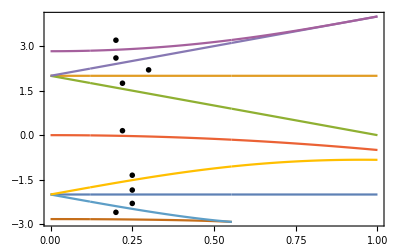

```mathematica
oqv=RootsGPoly[λ,a,b];
oqv[[1]]==oqv[[2]]&&oqv[[3]]==oqv[[4]]&&oqv[[6]]==oqv[[7]]
Plot[{oqv[[1]],oqv[[3]],oqv[[5]],oqv[[6]],oqv[[8]],oqv[[9]],oqv[[10]],oqv[[11]],oqv[[12]]},{α,0,1},PlotRange->All,
Frame->True,BaseStyle->{FontFamily->"Times",FontSize->15},PlotRangePadding->0.01,
Frame->{{True,False},{True,False}},
FrameStyle->Directive[Black,Thickness[.004]],FrameTicksStyle->Directive[Black,Thick],FrameLabel->{MaTeX["\\alpha",Magnification->1.5],MaTeX["\\mathrm{roots}",Magnification->1.5]},Epilog->{
Text[MaTeX["12","Preamble"->{"\\usepackage{bm}"},Magnification->0.8],{0.2,3.2}],
Text[MaTeX["11","Preamble"->{"\\usepackage{bm}"},Magnification->0.8],{0.25,-1.35}],
Text[MaTeX["10","Preamble"->{"\\usepackage{bm}"},Magnification->0.8],{0.25,-2.3}],
Text[MaTeX["9","Preamble"->{"\\usepackage{bm}"},Magnification->0.8],{0.2,-2.6}],
Text[MaTeX["8","Preamble"->{"\\usepackage{bm}"},Magnification->0.8],{0.2,2.6}],
Text[MaTeX["6,7","Preamble"->{"\\usepackage{bm}"},Magnification->0.8],{0.22,.15}],
Text[MaTeX["5","Preamble"->{"\\usepackage{bm}"},Magnification->0.8],{0.22,1.75}],
Text[MaTeX["3,4","Preamble"->{"\\usepackage{bm}"},Magnification->0.8],{0.3,2.2}],
Text[MaTeX["1,2","Preamble"->{"\\usepackage{bm}"},Magnification->0.8],{0.25,-1.85}]
}
]
```

#### via the spectrum of 𝒞[a^*(α),a^*(α),α,α] with optimal a^* (without Groebner basis)

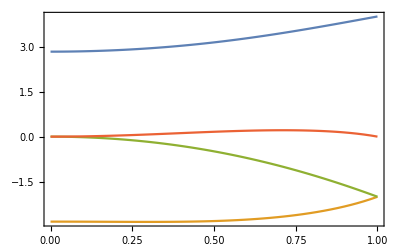

```mathematica
Plot[{Eigenvalues[𝒞[oAsett[α],oAsett[α],α]][[1]],Eigenvalues[𝒞[oAsett[α],oAsett[α],α]][[2]],Eigenvalues[𝒞[oAsett[α],oAsett[α],α]][[3]],Eigenvalues[𝒞[oAsett[α],oAsett[α],α]][[4]]},{α,0,1},PlotRange->All,
Frame->True,BaseStyle->{FontFamily->"Times",FontSize->15},PlotRangePadding->0,Frame->{{True,False},{True,False}},FrameStyle->Directive[Black,Thickness[.004]],FrameTicksStyle->Directive[Black,Thick],FrameLabel->{MaTeX["\\alpha",Magnification->1.5],Rotate[MaTeX["\\lambda",Magnification->1.5],-π/2]}(*,Epilog->{
Text[MaTeX["Happy\, marriage","Preamble"->{"\\usepackage{bm}"},Magnification->1.1],{.5,.8}]
}*)
]
```

The expression of these eigenvalues is λ→±_t(√ζ)/2±_s 1/2 √(κ∓_t(2 γ_1)/(√ζ))(see the sec. Analytical expression). 
The largest function (blue) corresponds to the 12th root listed inRootsGPoly[λ,a,b] (in purple from the other plot). 
The non-degeneracy in the eigenvalues selftest the eigenvector (see optimal quantum state in the next section)

### 2.2 Optimal Alice=Bob settings

```mathematica
(*Are the optimal Alice's settings the same of Bob's? The Output below shows that it is True*)RootsGPoly[a,λ,b]==RootsGPoly[b,a,λ]
```

True

#### With the Groebner basis (we do not use this approach)

```mathematica
As=RootsGPoly[a,λ,b];
```

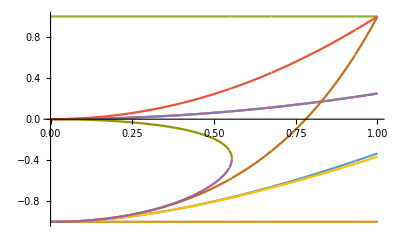

```mathematica
Plot[As,{α,0,1}]
```

#### Without the Groebner basis (we use this approach)

```mathematica
oAs[α_,β_:α]:=Module[{roots,sol},
roots=Solve[D[CharacteristicPolynomial[𝒞[a,a,α,β],λ], a]==0,a];
Array[a/.roots[[#]]&,Length[roots]]
]
oAs[α]
oAsett[α_]:=1/8 (-4+3 α^2+√(16+9 α^4+8 α^2(2 oqv[[12]]-1)))
```

{1,1/8 (-4+3 α^2-√(16-8 α^2+9 α^4+16 α^2 λ)),1/8 (-4+3 α^2+√(16-8 α^2+9 α^4+16 α^2 λ))}

The following plot takes into account the optimal quantum value.

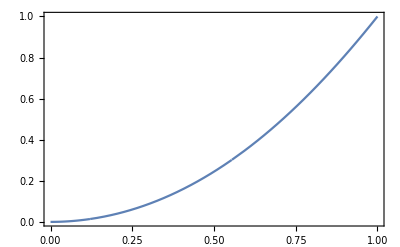

```mathematica
Plot[oAsett[α],{α,0,1},
Frame->True,BaseStyle->{FontFamily->"Times",FontSize->15},PlotRangePadding->0,Frame->{{True,False},{True,False}},FrameStyle->Directive[Black,Thickness[.004]],FrameTicksStyle->Directive[Black,Thick],FrameLabel->{MaTeX["\\alpha",Magnification->1.5],Rotate[MaTeX["\\cos(\\theta_A)",Magnification->1.5],0]}(*,Epilog->{
Text[MaTeX["Happy\, marriage","Preamble"->{"\\usepackage{bm}"},Magnification->1.1],{0.2,.8}]
}*)
]
```

### 2.3 Comparison between ideal and noisy CHSH

In this section we want to realize a plot that compare 𝒞[a,b,0,0] (perfect detectors) and 𝒞[a,b,α,β] (imperfect detectors) computed on the optimal state at each value of α and β. We take the optimal state ψ in dataψ[αindex,βindex] pay attention at which value of αindex,βindex maps to the values of α and β. Then we compute the functional and the marginal:
1	  vC0[α,β,0]=⟨𝒞[a,b,0,0]⟩_(ψ(α,β)) and vC1[α,β,1] =⟨𝒞[a,b,α,β]⟩_(ψ(α,β))  and LR[α,β]=⟨σ_3⊗σ_0+σ_0⊗σ_3⟩_(ψ(α,β)) all in v𝒞[α,β,0]
2	vC1[α,β]=2/(2+α)2/(2+β)⟨𝒞[a,b,0,0]⟩_(ψ(α,β))+2(1-2/(2+α))(1-2/(2+β))+[(1-2/(2+α))2/(2+β)+2/(2+α)(1-2/(2+β))]LR[α,β] and LR1[α,β]=√(2/(2+β)2/(2+α))LR[α,β]+(1-2/(2+α))+(1-2/(2+β)) as η_a→2/(2+α) all in v𝒞[α,β,1]
similarly to the previous version of the code:

LRVal1[α_,η_]:=η LRVal[α]+(1-η)2
CHSHVal1[α_,η_]:=η^2 CHSHVal[α]+(1-η)^2 2+2(1-η)(η)LRVal[α]

```mathematica
v𝒞[α_,β_]:=Module[{max0,abmax,eigesys,pos,ψ,v𝒞0,v𝒞1,LR,v𝒞01,v𝒞11,LR1,LRVal,CHSHVal},
(*compute the optimal a and b*)
max0=NMaximize[{Re[cQ[a,b,α,β]][[1]],0<=a<=1,0<=b<=1},{a,b}];
abmax={a,b}/.max0[[2]];
(*compute ψ*)
eigesys=Eigensystem[𝒞@@Join[abmax,{α,β}]];
pos=Flatten[PositionLargest[eigesys[[1]]]];
(*the optimal state is the eigenstate of 𝒞[a^*,b^*,α,β] at optimal a^*,b^* in abmax given at input α, β.*)
ψ=eigesys[[2,pos]][[1]];
v𝒞0=⟨ψ,𝒞@@Join[abmax,{0,0}].ψ⟩;
(*local randomness*)
LR=⟨ψ,(Subscript[σ, 3]⊙Subscript[σ, 0]+Subscript[σ, 0]⊙Subscript[σ, 3]).ψ⟩;
{LR,v𝒞0}
]
v𝒞1[α_,β_,ηa_,ηb_]:=Module[{LR,v𝒞0,LR1,v𝒞01},
{LR,v𝒞0}=v𝒞[α,β];

LR1=√(ηa ηb) LR+(1-ηa)+(1-ηb);
v𝒞01=ηa ηb v𝒞0+2(1-ηa)(1-ηb)+((1-ηa)ηb+(1-ηb)ηa)LR;
{LR1,v𝒞01}
]
v𝒞2[α_,β_,ηa_,ηb_]:=Module[{LR,v𝒞0,v𝒞LR},
{LR,v𝒞LR}=v𝒞[α,β];
{LR,2(1/ηa+1/ηb-1)-(1/ηa(1-ηa)+1/ηb(1-ηb))LR}
]
```

```mathematica
v𝒞2[.1,.1,0.85,0.85]
```

{0.242111,2.53498}

```mathematica
{Row[{Dynamic[α],"/",-1}],ProgressIndicator[Dynamic[α],{-1,1}]}
```

{/-1,}

```mathematica
list1=Table[v𝒞[α,α],{α,-1,1,0.005}];
```

```mathematica
list2=Table[v𝒞1[α,α,0.85,0.85],{α,-1,1,0.005}];
```

```mathematica
list3=Table[v𝒞2[α,α,0.85,0.85],{α,-1,1,0.005}];
```

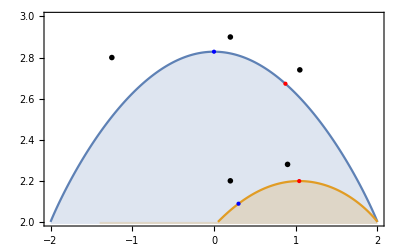

```mathematica
lp1=ListPlot[{list1,list2},Filling->Axis,Joined->True,PlotRange->{2,3},PlotRangePadding->0.01,Frame->True,
FrameStyle->Directive[Black,Thickness[.004]],FrameTicksStyle->Directive[Black,Thick],FrameLabel->{MaTeX["\\langle A_0\\rangle+\\langle B_0\\rangle","Preamble"->{"\\usepackage{bm}"},Magnification->1.5],MaTeX["C(\\bm{p})","Preamble"->{"\\usepackage{bm}"},Magnification->1.5]},Frame->True,
Epilog->{
{Blue,PointSize@Large,Point[{v𝒞[0,0],v𝒞1[0,0,.85,.85]}]},{Red,PointSize@Large,Point[{v𝒞[2(1-.85)/(.85),2(1-.85)/(.85)],v𝒞1[2(1-.85)/(.85),2(1-.85)/(.85),.85,.85]}]},{Text[MaTeX["\\eta_A,\\eta_B=0.85",Magnification->1.5],{-1.25,2.8}]},
{Text[MaTeX["\\bm{p}_\\mathrm{iso}","Preamble"->{"\\usepackage{bm}"},Magnification->1.5],{0.2,2.9}]},
{Text[MaTeX["\\bm{p}_\\mathrm{tilted}","Preamble"->{"\\usepackage{bm}"},Magnification->1.5],{1.05,2.74}]},{Text[MaTeX["\\tilde{\\bm{p}}_\\mathrm{iso}","Preamble"->{"\\usepackage{bm}"},Magnification->1.5],{0.2,2.2}]},
{Text[MaTeX["\\tilde{\\bm{p}}_\\mathrm{tilted}","Preamble"->{"\\usepackage{bm}"},Magnification->1.5],{0.9,2.28}]}
}
]
```

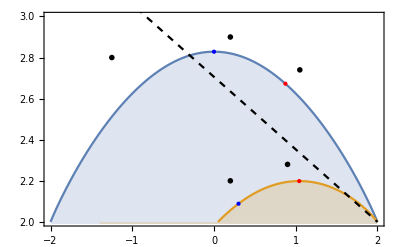

```mathematica
Show[{lp1,ListPlot[list3,Joined->True,PlotStyle->{Dashed,Black}]}]
```

## 3. Not equal inefficiency detectors α≠β

### 3.1 Optimal quantum value c_Q ( via Groebner - p(λ)=RootsGPoly[λ,a,b,β]=∑_(i=1)^deg c_i(α,β)λ^i )

```mathematica
(*oqvβ contains the roots of p(λ)= ∑_(k=0)^11 Subscript[c, k](α,β)λ^k*)
oqvβ=RootsGPoly[λ,a,b,β];
```

```mathematica
oqvβmax[α0_,β0_]:=Max[Re/@oqvβ]
cqplot=Plot3D[oqvβmax[α,β],{α,0,2},{β,0,2-α},PlotRange->All,
BaseStyle->{FontFamily->"Times",FontSize->15},
(*TicksStyle->Directive[Black,Thick],*)AxesLabel->{MaTeX["\\alpha",Magnification->1.5],MaTeX["\\beta",Magnification->1.5],MaTeX["c_{\\mathcal{Q}}",Magnification->1.5]},Boxed->True
]
```

-Graphics3D-

TECHNICAL DETAILS - In the following, we plot the optimal quantum value oqv obtained from Groebner elimination procedure with RootsGPoly[λ,a,b,β=α], and compare with the 10^th and 12^th root of oqvβ=RootsGPoly[λ,a,b,β≠α], with coeffients c_k(α,β), computed at β=α. We observe that at α=2/(√13),  the trend of the 12^th roots goes to the 10^th one.

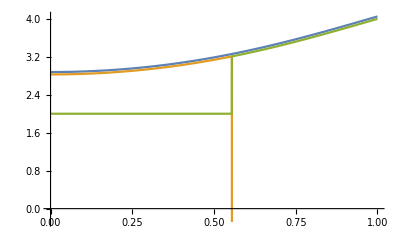

```mathematica
Plot[{oqv[[12]]+0.05,Re[oqvβ[[12]]/.β->α],Re[oqvβ[[10]]/.β->α]},{α,0,1}]
```

```mathematica
2/(√13)//N
```

0.5547

```mathematica
(*the change is α=0.55473 *)
Table[Re[{oqv[[12]],oqvβ[[10]]/.β->α,oqvβ[[12]]/.β->α}],{α,0.55470,0.55475,0.00001}]
```

{{3.20868,2.,3.20868},{3.20869,2.,3.20869},{3.20871,2.,3.20871},{3.20872,3.20872,-2.9231},{3.20873,3.20873,-2.92311},{3.20875,3.20875,-2.92311}}

Now we plot the optimal quantum value for β ≠ α taking the maximum between the 10th and 12th root of oqvβ.

```mathematica
oqvβf[α0_,β0_]:=Module[{α=α0,β=β0,oqvβ1,oqvβ2},
oqvβ1[α_,β_]:=Root[-512+128 α^2+32 α^4-8 α^6+128 β^2-400 α^2 β^2+48 α^4 β^2+27 α^6 β^2+32 β^4+48 α^2 β^4-54 α^4 β^4-8 β^6+27 α^2 β^6+(-576 α β+160 α^3 β+60 α^5 β+160 α β^3-168 α^3 β^3+60 α β^5) #1+(320+96 α^2+20 α^4+96 β^2-64 α^2 β^2-6 α^4 β^2+20 β^4-6 α^2 β^4) #1^2+(96 α β-24 α^3 β-24 α β^3+8 α^3 β^3) #1^3+(-64-16 α^2-16 β^2+11 α^2 β^2) #1^4-4 α β #1^5+4 #1^6&,4];
oqvβ2[α_,β_]:=Root[-512+128 α^2+32 α^4-8 α^6+128 β^2-400 α^2 β^2+48 α^4 β^2+27 α^6 β^2+32 β^4+48 α^2 β^4-54 α^4 β^4-8 β^6+27 α^2 β^6+(-576 α β+160 α^3 β+60 α^5 β+160 α β^3-168 α^3 β^3+60 α β^5) #1+(320+96 α^2+20 α^4+96 β^2-64 α^2 β^2-6 α^4 β^2+20 β^4-6 α^2 β^4) #1^2+(96 α β-24 α^3 β-24 α β^3+8 α^3 β^3) #1^3+(-64-16 α^2-16 β^2+11 α^2 β^2) #1^4-4 α β #1^5+4 #1^6&,6];

Max[{Re[oqvβ1[α,β]],Re[oqvβ2[α,β]]}]
]
```

Here we show that it is enough to consider only the 10^th and 12^th root since the plot show that oqvβmax=max{oqvβ[[1]],...,oqvβ[[12]]}=oqvβf=max{oqvβ[[10]],oqvβ[[12]]}.

```mathematica
Plot3D[{oqvβf[α,β],oqvβmax[α,β]},{α,0,2},{β,0,2-α}]
```

-Graphics3D-

### 3.2 optimal Alice & Bob settings

#### without Groebner basis - NOT USED

Here we try to generalize the optimal settings with Groebner basis, but the solution need to be carefully adapted, However, we are not using this section but we leave it here to highlight the contrast with the related section 2.2 of optimal setting in the case of α=β.

```mathematica
Solve[{D[#, a],D[#, b]}&[CharacteristicPolynomial[𝒞[a,b,α,β],λ]]==0,{a,b}]
```

{{a→1,b→(4-2 α^2-β^2-α β λ)/(-4+β^2)},{a→(16-4 α^2-12 β^2+3 α^2 β^2-√(-4+α^2) √(-4+β^2) √(16-4 α^2-4 β^2+9 α^2 β^2+16 α β λ))/(2 (-16+4 α^2)),b→1/(4-β^2)(α^2+32/(-16+4 α^2)-(16 α^2)/(-16+4 α^2)+(2 α^4)/(-16+4 α^2)-β^2-(24 β^2)/(-16+4 α^2)+(12 α^2 β^2)/(-16+4 α^2)-(3 α^4 β^2)/(2 (-16+4 α^2))-(2 √(-4+α^2) √(-4+β^2) √(16-4 α^2-4 β^2+9 α^2 β^2+16 α β λ))/(-16+4 α^2)+(α^2 √(-4+α^2) √(-4+β^2) √(16-4 α^2-4 β^2+9 α^2 β^2+16 α β λ))/(2 (-16+4 α^2)))},{a→(16-4 α^2-12 β^2+3 α^2 β^2+√(-4+α^2) √(-4+β^2) √(16-4 α^2-4 β^2+9 α^2 β^2+16 α β λ))/(2 (-16+4 α^2)),b→1/(4-β^2)(α^2+32/(-16+4 α^2)-(16 α^2)/(-16+4 α^2)+(2 α^4)/(-16+4 α^2)-β^2-(24 β^2)/(-16+4 α^2)+(12 α^2 β^2)/(-16+4 α^2)-(3 α^4 β^2)/(2 (-16+4 α^2))+(2 √(-4+α^2) √(-4+β^2) √(16-4 α^2-4 β^2+9 α^2 β^2+16 α β λ))/(-16+4 α^2)-(α^2 √(-4+α^2) √(-4+β^2) √(16-4 α^2-4 β^2+9 α^2 β^2+16 α β λ))/(2 (-16+4 α^2)))},{a→1,b→1},{a→(4-α^2-2 β^2-α β λ)/(-4+α^2),b→1}}

```mathematica
oABs[α_,β_]:=Module[{roots},
roots=Solve[{D[#, a],D[#, b]}&[CharacteristicPolynomial[𝒞[a,b,α,β],λ]]==0,{a,b}];
Array[{a,b}/.roots[[#]]&,Length[roots]]
]
```

This list of value {a,b} generalize the expression oAs[α,α]={1,1/8 (-4+3 α^2-√(16-8 α^2+9 α^4+16 α^2 λ)),1/8 (-4+3 α^2+√(16-8 α^2+9 α^4+16 α^2 λ))} from the previous section α=β.

```mathematica
oABs[α,β]
```

{{1,(4-2 α^2-β^2-α β λ)/(-4+β^2)},{(16-4 α^2-12 β^2+3 α^2 β^2-√(-4+α^2) √(-4+β^2) √(16-4 α^2-4 β^2+9 α^2 β^2+16 α β λ))/(2 (-16+4 α^2)),1/(4-β^2)(α^2+32/(-16+4 α^2)-(16 α^2)/(-16+4 α^2)+(2 α^4)/(-16+4 α^2)-β^2-(24 β^2)/(-16+4 α^2)+(12 α^2 β^2)/(-16+4 α^2)-(3 α^4 β^2)/(2 (-16+4 α^2))-1/(-16+4 α^2)2 √(-4+α^2) √(-4+β^2) √(16-4 α^2-4 β^2+9 α^2 β^2+16 α β λ)+(α^2 √(-4+α^2) √(-4+β^2) √(16-4 α^2-4 β^2+9 α^2 β^2+16 α β λ))/(2 (-16+4 α^2)))},{(16-4 α^2-12 β^2+3 α^2 β^2+√(-4+α^2) √(-4+β^2) √(16-4 α^2-4 β^2+9 α^2 β^2+16 α β λ))/(2 (-16+4 α^2)),1/(4-β^2)(α^2+32/(-16+4 α^2)-(16 α^2)/(-16+4 α^2)+(2 α^4)/(-16+4 α^2)-β^2-(24 β^2)/(-16+4 α^2)+(12 α^2 β^2)/(-16+4 α^2)-(3 α^4 β^2)/(2 (-16+4 α^2))+1/(-16+4 α^2)2 √(-4+α^2) √(-4+β^2) √(16-4 α^2-4 β^2+9 α^2 β^2+16 α β λ)-(α^2 √(-4+α^2) √(-4+β^2) √(16-4 α^2-4 β^2+9 α^2 β^2+16 α β λ))/(2 (-16+4 α^2)))},{1,1},{(4-α^2-2 β^2-α β λ)/(-4+α^2),1}}

#### via Groebner basis

p(a)=RootsGPoly[a,λ,b,β]=∑_(i=1)^deg c_i(α,β)λ^i 
p(b)=RootsGPoly[b,λ,a,β]=∑_(i=1)^deg c_i(α,β)λ^i

```mathematica
(*It takes around 30sec*)
Asβ[α_,β_]=RootsGPoly[a,λ,b,β];(*==RootsGPoly[b,a,λ]*)
```

```mathematica
Bsβ[α_,β_]=RootsGPoly[b,λ,a,β];(*==RootsGPoly[b,a,λ]*)
```

```mathematica
oAsβ[α_,β_]:=Module[{sol},
sol=Asβ[α,β][[8;;13]];

Piecewise[{{Max[Re[sol]], α+β<2}, {100, α+β>=2}}]
]
oBsβ[α_,β_]:=Module[{sol},
sol=Bsβ[α,β][[8;;13]];

Piecewise[{{Max[Re[sol]], α+β<2}, {100, α+β>=2}}]
]
```

```mathematica
(*All these plot will be shown at the end of the project*)
```

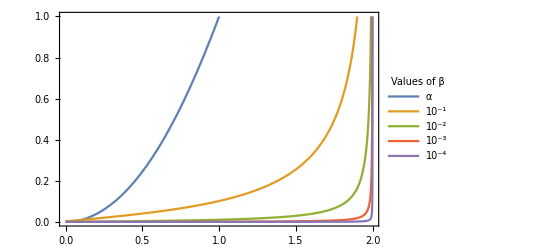

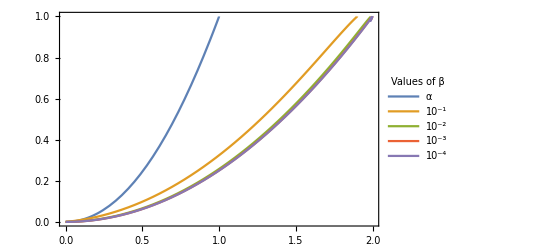

-Graphics3D-

-Graphics3D-

```mathematica
ca2D=Plot[{oAsβ[α,α],oAsβ[α,10^-1],oAsβ[α,10^-2],oAsβ[α,10^-3],oAsβ[α,10^-4]},{α,0,2},PlotRange->{0,1},Frame->True,BaseStyle->{FontFamily->"Times",FontSize->15},PlotRangePadding->0.05,Frame->{{True,False},{True,False}},FrameStyle->Directive[Black,Thickness[.001]],FrameTicksStyle->Directive[Black,Thin],FrameLabel->{MaTeX["\\alpha",Magnification->1.5],Rotate[MaTeX["c_{A}",Magnification->1.5],0]},
PlotLegends->Placed[LineLegend[{"α","10^-1","10^-2","10^-3","10^-4"}(*,LegendFunction->"Frame"*),LegendLabel->"Values of β",LegendMarkers->Automatic,LabelStyle->{FontFamily->"Times",FontSize->14}],{Left,Top}  (*Adjust this placement as needed*)]]
cb2D=Plot[{oBsβ[α,α],oBsβ[α,10^-1],oBsβ[α,10^-2],oBsβ[α,10^-3],oBsβ[α,10^-4]},{α,0,2},PlotRange->{0,1},Frame->True,BaseStyle->{FontFamily->"Times",FontSize->15},PlotRangePadding->0.05,Frame->{{True,False},{True,False}},FrameStyle->Directive[Black,Thickness[.001]],FrameTicksStyle->Directive[Black,Thin],FrameLabel->{MaTeX["\\alpha",Magnification->1.5],Rotate[MaTeX["c_{B}",Magnification->1.5],0]},
PlotLegends->Placed[LineLegend[{"α","10^-1","10^-2","10^-3","10^-4"}(*,LegendFunction->"Frame"*),LegendLabel->"Values of β",LegendMarkers->Automatic,LabelStyle->{FontFamily->"Times",FontSize->14}],{Left,Top}  ]]
ca3D=Plot3D[oAsβ[α,β],{α,0,2},{β,0,2-α},PlotRange->{0,1},BaseStyle->{FontFamily->"Times",FontSize->15},PlotRangePadding->0.05,AxesLabel->{MaTeX["\\alpha",Magnification->1.5],MaTeX["\\beta",Magnification->1.5],Rotate[MaTeX["c_{A}",Magnification->1.5],π/2]},MeshFunctions->{#2&},Mesh->30 ,
ColorFunction->Function[{x,y,z},RGBColor[1,0.8,0.8]],ColorFunctionScaling->True
]
cb3D=Plot3D[oBsβ[α,β],{α,0,2},{β,0,2-α},PlotRange->{0,1},BaseStyle->{FontFamily->"Times",FontSize->15},PlotRangePadding->0.05,AxesLabel->{MaTeX["\\alpha",Magnification->1.5],MaTeX["\\beta",Magnification->1.5],Rotate[MaTeX["c_{B}",Magnification->1.5],π/2]},MeshFunctions->{#2&},Mesh->30 ,
ColorFunction->Function[{x,y,z},RGBColor[0.8,0.8,1]],ColorFunctionScaling->True
]
```

### 3.3 Data by analytical optimal quantum value c_Q(a,b,α,β) and optimizing on settings a^* and b^* - USED AS DOUBLE CHECK

From the analytical expression of the eigenvalues (see the section analytical expression) we define cQ[a,b,α,β] the largest eigenvalue of the Bell function 𝒞[a,b,α,β] representing the optimal quantum value.

```mathematica
cQ[a_,b_,α_,β_]:=Module[{ζ,κ,γ,ξ},
Subscript[γ, 0]=(α^2-β^2)^2-8(α^2(a^2-a^2 b+b)+β^2(b^2-b^2 a+a)-2(b^2+a^2-a^2 b^2));
Subscript[γ, 1]=8α β(a b-a - b- 1);
Subscript[γ, 2]=-2(4+ α^2+β^2);
Subscript[γ, 3]=0;
Subscript[γ, 4]=1;
ξ=27 Subscript[γ, 1]^2-72 Subscript[γ, 0] Subscript[γ, 2]+2 Subscript[γ, 2]^3+√(-4 (12 Subscript[γ, 0]+Subscript[γ, 2]^2)^3+(27 Subscript[γ, 1]^2-72 Subscript[γ, 0] Subscript[γ, 2]+2 Subscript[γ, 2]^3)^2);
ζ=ξ^(1/3)/(3 2^(1/3))-(2 Subscript[γ, 2])/3+(2^(1/3) (12 Subscript[γ, 0]+Subscript[γ, 2]^2))/(3 ξ^(1/3));
κ=-ξ^(1/3)/(3 2^(1/3))-(4 Subscript[γ, 2])/3-(2^(1/3) (12 Subscript[γ, 0]+Subscript[γ, 2]^2))/(3 ξ^(1/3));
{(√ζ)/2+1/2 √(κ-2 Subscript[γ, 1]/(√ζ)),(√ζ)/2-1/2 √(κ-2 Subscript[γ, 1]/(√ζ)),-(√ζ)/2+1/2 √(κ+2 Subscript[γ, 1]/(√ζ)),-(√ζ)/2-1/2 √(κ+2 Subscript[γ, 1]/(√ζ))}
]
```

Now we want to maximize respect to a and b for all possible values of the efficiency 0<=α+β<2. We write on file.

#### write on file

This function input α,β and output {{a^*,b^*,α,β,λ_max},{a^*,b^*,α,β,λ_2},{a^*,b^*,α,β,λ_3},{a^*,b^*,α,β,λ_4}}, where a^*,b^* are the optimal settings.

```mathematica
listabλmax[α0_,β0_]:=Module[{λ4,max,α=α0,β=β0},
max=Table[NMaximize[{Re[cQ[a,b,α,β]][[i]],0<=a<=1,0<=b<=1},{a,b}],{i,4}];
Flatten[{{a,b}/.#[[2]],α,β,#[[1]]}]&/@max
]
```

```mathematica
{Row[{Dynamic[α],"/",2}],ProgressIndicator[Dynamic[α],{0,2}]}
{Row[{Dynamic[β],"/",2}],ProgressIndicator[Dynamic[β],{0,2}]}
```

{/2,}

{/2,}

```mathematica
list3dα=Table[listabλmax[α,α],{α,0,1,0.01}];
```

NMaximize::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

General::stop: Further output of NMaximize::cvmit will be suppressed during this calculation.

```mathematica
list3d=Table[listabλmax[α,β],{α,0,2,0.05},{β,0,2-α,0.05}];
```

NMaximize::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

General::stop: Further output of NMaximize::cvmit will be suppressed during this calculation.

```mathematica
savefiles1[list3d,"list-ab-alfabeta-eiges.txt"]
```

```mathematica
savefiles1[list3dα,"list-ab-alfaalfa-eiges.txt"]
```

#### read from the file

```mathematica
(*now we read from the file*)
SetDirectory[NotebookDirectory[]];
(*a,b,α,β,cQ*)
data=readlist["list-ab-alfabeta-eiges.txt"];
dataα=readlist["list-ab-alfaalfa-eiges.txt"];
```

The plot with Graphics3D simply show that there are respectively one points that is optimized on the other interval of possibility of a and b since these function gives the same result up to a period of 4.

```mathematica
(*data[[All,All,i]] for i=1,2,3,4 select the eigenvalue, i=1 is the largest.*)
```

{{{8.18458×10^-9,6.8583×10^-9,0.,0.,2.82843},{0.000624983,1.48677×10^-8,0.,0.05,2.82931},{0.00250003,2.04174×10^-8,0.,0.1,2.83196},{0.00562502,2.11917×10^-8,0.,0.15,2.83637},{0.00999999,0.,0.,0.2,2.84253},{0.015625,1.99278×10^-8,0.,0.25,2.85044},{0.0225,0.,0.,0.3,2.86007},{0.030625,0.,0.,0.35,2.87141},{0.04,0.,0.,0.4,2.88444},{0.0506251,1.32923×10^-8,0.,0.45,2.89914},{0.0625001,0.,0.,0.5,2.91548},{0.075625,1.7756×10^-8,0.,0.55,2.93343},{0.09,1.322×10^-8,0.,0.6,2.95296},{0.105625,9.51025×10^-9,0.,0.65,2.97405},{0.1225,1.34622×10^-8,0.,0.7,2.99666},{0.140625,0.,0.,0.75,3.02076},{0.16,3.51448×10^-8,0.,0.8,3.04631},{0.180625,2.38924×10^-9,0.,0.85,3.07327},{0.2025,6.85911×10^-8,0.,0.9,3.10161},{0.225625,6.84088×10^-8,0.,0.95,3.13129},{0.25,2.76829×10^-8,0.,1.,3.16228},{0.275625,8.16138×10^-8,0.,1.05,3.19453},{0.3025,2.96123×10^-8,0.,1.1,3.228},{0.330625,4.17221×10^-8,0.,1.15,3.26267},{0.36,1.27631×10^-7,0.,1.2,3.29848},{0.390625,2.51051×10^-8,0.,1.25,3.33542},{0.4225,3.46111×10^-7,0.,1.3,3.37343},{0.455625,3.38714×10^-8,0.,1.35,3.41248},{0.49,4.67806×10^-8,0.,1.4,3.45254},{0.525625,1.14231×10^-7,0.,1.45,3.49357},{0.5625,0.,0.,1.5,3.53553},{0.600625,1.41491×10^-7,0.,1.55,3.57841},{0.64,5.94173×10^-8,0.,1.6,3.62215},{0.680625,7.84847×10^-9,0.,1.65,3.66674},{0.7225,3.90722×10^-8,0.,1.7,3.71214},{0.765625,1.9755×10^-6,0.,1.75,3.75832},{0.81,2.985×10^-7,0.,1.8,3.80526},{0.855625,6.06562×10^-6,0.,1.85,3.85292},{0.9025,3.16063×10^-7,0.,1.9,3.90128},{0.950625,0.0000334718,0.,1.95,3.95032},{0.,1.,0.,2.,4.}},{{1.66131×10^-8,0.000624989,0.05,0.,2.82931},{0.00102922,0.0010292,0.05,0.05,2.83064},{0.00330835,0.00143486,0.05,0.1,2.83373},{0.00683739,0.00184347,0.05,0.15,2.83857},{0.0116163,0.00225658,0.05,0.2,2.84517},{0.0176451,0.00267584,0.05,0.25,2.85351},{0.0249237,0.0031029,0.05,0.3,2.86357},{0.0334522,0.00353969,0.05,0.35,2.87533},{0.0432306,0.00398804,0.05,0.4,2.88878},{0.0542587,0.00445005,0.05,0.45,2.90388},{0.0665366,0.00492799,0.05,0.5,2.92062},{0.0800642,0.00542439,0.05,0.55,2.93897},{0.0948416,0.00594211,0.05,0.6,2.9589},{0.110869,0.0064842,0.05,0.65,2.98036},{0.128145,0.00705416,0.05,0.7,3.00334},{0.146671,0.00765616,0.05,0.75,3.0278},{0.166447,0.00829481,0.05,0.8,3.0537},{0.187471,0.00897544,0.05,0.85,3.08101},{0.209745,0.00970437,0.05,0.9,3.10968},{0.233268,0.0104891,0.05,0.95,3.13969},{0.25804,0.0113382,0.05,1.,3.17098},{0.28406,0.0122625,0.05,1.05,3.20354},{0.311329,0.0132748,0.05,1.1,3.23731},{0.339845,0.0143907,0.05,1.15,3.27226},{0.369609,0.0156298,0.05,1.2,3.30835},{0.40062,0.0170164,0.05,1.25,3.34555},{0.432877,0.0185822,0.05,1.3,3.38382},{0.466379,0.0203673,0.05,1.35,3.42312},{0.501125,0.0224251,0.05,1.4,3.46341},{0.537114,0.024828,0.05,1.45,3.50467},{0.574342,0.0276753,0.05,1.5,3.54687},{0.612807,0.0311088,0.05,1.55,3.58995},{0.652504,0.0353378,0.05,1.6,3.63391},{0.693427,0.0406842,0.05,1.65,3.67869},{0.735563,0.0476681,0.05,1.7,3.72428},{0.778893,0.0571985,0.05,1.75,3.77065},{0.823381,0.0710059,0.05,1.8,3.81776},{0.868951,0.092871,0.05,1.85,3.86559},{0.915414,0.132994,0.05,1.9,3.91411},{0.962084,0.23257,0.05,1.95,3.96329}},{{0.,0.00250002,0.1,0.,2.83196},{0.00143485,0.00330833,0.1,0.05,2.83373},{0.0041193,0.00411929,0.1,0.1,2.83725},{0.00805334,0.004936,0.1,0.15,2.84254},{0.013237,0.00576149,0.1,0.2,2.84957},{0.0196701,0.00659899,0.1,0.25,2.85833},{0.0273527,0.00745202,0.1,0.3,2.86881},{0.0362848,0.00832398,0.1,0.35,2.88099},{0.0464662,0.00921876,0.1,0.4,2.89484},{0.0578969,0.0101405,0.1,0.45,2.91035},{0.0705767,0.0110936,0.1,0.5,2.92749},{0.0845056,0.0120831,0.1,0.55,2.94622},{0.0996833,0.0131144,0.1,0.6,2.96652},{0.11611,0.0141936,0.1,0.65,2.98836},{0.133784,0.0153277,0.1,0.7,3.0117},{0.152707,0.0165243,0.1,0.75,3.0365},{0.172878,0.0177927,0.1,0.8,3.06274},{0.194296,0.0191431,0.1,0.85,3.09038},{0.216961,0.0205875,0.1,0.9,3.11937},{0.240872,0.0221404,0.1,0.95,3.14969},{0.266029,0.0238183,0.1,1.,3.18128},{0.29243,0.0256416,0.1,1.05,3.21413},{0.320075,0.0276344,0.1,1.1,3.24818},{0.348962,0.0298264,0.1,1.15,3.2834},{0.37909,0.0322542,0.1,1.2,3.31975},{0.410457,0.0349635,0.1,1.25,3.3572},{0.44306,0.0380125,0.1,1.3,3.39571},{0.476895,0.0414755,0.1,1.35,3.43524},{0.51196,0.0454503,0.1,1.4,3.47576},{0.548247,0.0500682,0.1,1.45,3.51723},{0.585749,0.0555085,0.1,1.5,3.55963},{0.624457,0.0620232,0.1,1.55,3.60291},{0.664354,0.06998,0.1,1.6,3.64706},{0.705418,0.0799361,0.1,1.65,3.69202},{0.747615,0.0927793,0.1,1.7,3.73779},{0.790888,0.110021,0.1,1.75,3.78431},{0.835136,0.134467,0.1,1.8,3.83158},{0.880161,0.172019,0.1,1.85,3.87955},{0.925495,0.237762,0.1,1.9,3.92821}},{{4.80015×10^-9,0.005625,0.15,0.,2.83637},{0.00184346,0.00683741,0.15,0.05,2.83857},{0.00493597,0.00805334,0.15,0.1,2.84254},{0.00927757,0.00927756,0.15,0.15,2.84825},{0.0148681,0.0105147,0.15,0.2,2.85571},{0.0217078,0.0117696,0.15,0.25,2.86489},{0.0297963,0.0130473,0.15,0.3,2.87579},{0.0391336,0.0143531,0.15,0.35,2.88837},{0.0497196,0.0156926,0.15,0.4,2.90263},{0.061554,0.017072,0.15,0.45,2.91853},{0.0746367,0.018498,0.15,0.5,2.93605},{0.0889672,0.0199776,0.15,0.55,2.95516},{0.104545,0.0215189,0.15,0.6,2.97582},{0.121371,0.0231311,0.15,0.65,2.99802},{0.139443,0.0248241,0.15,0.7,3.0217},{0.15876,0.0266094,0.15,0.75,3.04685},{0.179324,0.0284999,0.15,0.8,3.07341},{0.201131,0.0305111,0.15,0.85,3.10137},{0.224182,0.0326601,0.15,0.9,3.13067},{0.248476,0.0349675,0.15,0.95,3.16128},{0.274009,0.0374575,0.15,1.,3.19316},{0.300782,0.040159,0.15,1.05,3.22628},{0.328791,0.0431069,0.15,1.1,3.26059},{0.358035,0.046343,0.15,1.15,3.29606},{0.388509,0.0499196,0.15,1.2,3.33266},{0.42021,0.0539009,0.15,1.25,3.37034},{0.453132,0.0583687,0.15,1.3,3.40908},{0.487269,0.0634273,0.15,1.35,3.44882},{0.522613,0.0692127,0.15,1.4,3.48955},{0.559153,0.0759057,0.15,1.45,3.53122},{0.596874,0.0837523,0.15,1.5,3.5738},{0.635756,0.093096,0.15,1.55,3.61727},{0.675772,0.104432,0.15,1.6,3.66158},{0.71688,0.118504,0.15,1.65,3.70671},{0.759018,0.13648,0.15,1.7,3.75262},{0.802087,0.160321,0.15,1.75,3.79929},{0.845916,0.193596,0.15,1.8,3.84668},{0.89018,0.243623,0.15,1.85,3.89477}},{{0.,0.01,0.2,0.,2.84253},{0.00225658,0.0116163,0.2,0.05,2.84517},{0.00576149,0.0132369,0.2,0.1,2.84957},{0.0105147,0.0148682,0.2,0.15,2.85571},{0.0165163,0.0165163,0.2,0.2,2.86358},{0.0237661,0.0181876,0.2,0.25,2.87318},{0.032264,0.0198889,0.2,0.3,2.88448},{0.0420099,0.0216272,0.2,0.35,2.89747},{0.0530035,0.0234099,0.2,0.4,2.91212},{0.0652445,0.0252451,0.2,0.45,2.9284},{0.0787325,0.0271416,0.2,0.5,2.9463},{0.0934671,0.0291088,0.2,0.55,2.96577},{0.109448,0.0311573,0.2,0.6,2.98679},{0.126673,0.0332987,0.2,0.65,3.00933},{0.145143,0.0355464,0.2,0.7,3.03335},{0.164857,0.037915,0.2,0.75,3.05882},{0.185812,0.0404217,0.2,0.8,3.0857},{0.208009,0.0430859,0.2,0.85,3.11395},{0.231444,0.0459301,0.2,0.9,3.14354},{0.256116,0.0489809,0.2,0.95,3.17443},{0.282022,0.0522693,0.2,1.,3.20659},{0.30916,0.0558323,0.2,1.05,3.23996},{0.337526,0.0597142,0.2,1.1,3.27453},{0.367115,0.0639687,0.2,1.15,3.31024},{0.397923,0.0686618,0.2,1.2,3.34706},{0.429942,0.0738751,0.2,1.25,3.38496},{0.463165,0.0797111,0.2,1.3,3.4239},{0.497581,0.0863009,0.2,1.35,3.46385},{0.533177,0.0938144,0.2,1.4,3.50476},{0.569936,0.102476,0.2,1.45,3.54661},{0.607836,0.11259,0.2,1.5,3.58936},{0.646846,0.124577,0.2,1.55,3.63299},{0.686924,0.139041,0.2,1.6,3.67745},{0.728009,0.15688,0.2,1.65,3.72271},{0.770009,0.179493,0.2,1.7,3.76875},{0.812783,0.209197,0.2,1.75,3.81554},{0.85609,0.250151,0.2,1.8,3.86304}},{{0.,0.015625,0.25,0.,2.85044},{0.00267586,0.017645,0.25,0.05,2.85351},{0.00659904,0.0196701,0.25,0.1,2.85833},{0.0117696,0.0217078,0.25,0.15,2.86489},{0.0181876,0.0237661,0.25,0.2,2.87318},{0.0258529,0.025853,0.25,0.25,2.88319},{0.0347655,0.0279768,0.25,0.3,2.89489},{0.0449249,0.0301462,0.25,0.35,2.90827},{0.056331,0.0323706,0.25,0.4,2.9233},{0.0689831,0.03466,0.25,0.45,2.93996},{0.0828809,0.037025,0.25,0.5,2.95821},{0.0980236,0.0394774,0.25,0.55,2.97804},{0.11441,0.0420303,0.25,0.6,2.99941},{0.13204,0.0446979,0.25,0.65,3.02228},{0.150911,0.0474963,0.25,0.7,3.04662},{0.171022,0.0504438,0.25,0.75,3.0724},{0.192372,0.0535611,0.25,0.8,3.09958},{0.214958,0.056872,0.25,0.85,3.12812},{0.238778,0.0604037,0.25,0.9,3.15798},{0.263828,0.0641884,0.25,0.95,3.18914},{0.290106,0.0682638,0.25,1.,3.22155},{0.317606,0.0726742,0.25,1.05,3.25517},{0.346324,0.0774731,0.25,1.1,3.28996},{0.376253,0.082725,0.25,1.15,3.3259},{0.407386,0.0885086,0.25,1.2,3.36293},{0.439713,0.0949214,0.25,1.25,3.40103},{0.473223,0.102085,0.25,1.3,3.44016},{0.507902,0.110155,0.25,1.35,3.48029},{0.54373,0.119333,0.25,1.4,3.52137},{0.580685,0.12988,0.25,1.45,3.56338},{0.618735,0.142154,0.25,1.5,3.60628},{0.657839,0.156644,0.25,1.55,3.65004},{0.697938,0.17405,0.25,1.6,3.69463},{0.738953,0.195402,0.25,1.65,3.74001},{0.780762,0.222296,0.25,1.7,3.78616},{0.823178,0.257349,0.25,1.75,3.83304}},{{2.65079×10^-8,0.0225,0.3,0.,2.86007},{0.00310293,0.0249237,0.3,0.05,2.86357},{0.00745201,0.0273527,0.3,0.1,2.86881},{0.0130473,0.0297963,0.3,0.15,2.87579},{0.0198889,0.032264,0.3,0.2,2.88448},{0.0279767,0.0347655,0.3,0.25,2.89489},{0.0373106,0.0373106,0.3,0.3,2.90698},{0.0478902,0.03991,0.3,0.35,2.92074},{0.0597152,0.0425746,0.3,0.4,2.93615},{0.0727849,0.0453164,0.3,0.45,2.95317},{0.0870986,0.0481481,0.3,0.5,2.97178},{0.102655,0.0510836,0.3,0.55,2.99195},{0.119454,0.0541382,0.3,0.6,3.01364},{0.137492,0.057329,0.3,0.65,3.03683},{0.15677,0.0606749,0.3,0.7,3.06148},{0.177283,0.0641974,0.3,0.75,3.08756},{0.199032,0.0679206,0.3,0.8,3.11502},{0.222011,0.0718725,0.3,0.85,3.14384},{0.246218,0.0760851,0.3,0.9,3.17396},{0.271648,0.0805958,0.3,0.95,3.20537},{0.298298,0.0854483,0.3,1.,3.23802},{0.32616,0.0906944,0.3,1.05,3.27186},{0.355229,0.0963961,0.3,1.1,3.30687},{0.385495,0.102628,0.3,1.15,3.34301},{0.416949,0.109481,0.3,1.2,3.38024},{0.449578,0.117067,0.3,1.25,3.41852},{0.483367,0.125526,0.3,1.3,3.45783},{0.518297,0.135035,0.3,1.35,3.49811},{0.554343,0.145825,0.3,1.4,3.53935},{0.591476,0.158193,0.3,1.45,3.58149},{0.629655,0.172544,0.3,1.5,3.62453},{0.668827,0.18943,0.3,1.55,3.66841},{0.708919,0.209634,0.3,1.6,3.7131},{0.749828,0.234308,0.3,1.65,3.75858},{0.791405,0.265219,0.3,1.7,3.80481}},{{5.46444×10^-10,0.030625,0.35,0.,2.87141},{0.00353971,0.0334522,0.35,0.05,2.87533},{0.00832394,0.0362848,0.35,0.1,2.88099},{0.0143531,0.0391336,0.35,0.15,2.88837},{0.0216271,0.0420099,0.35,0.2,2.89747},{0.0301462,0.0449249,0.35,0.25,2.90827},{0.03991,0.0478903,0.35,0.3,2.92074},{0.0509182,0.0509182,0.35,0.35,2.93488},{0.0631703,0.0540216,0.35,0.4,2.95064},{0.0766655,0.0572141,0.35,0.45,2.96802},{0.0914028,0.0605105,0.35,0.5,2.98697},{0.107381,0.063927,0.35,0.55,3.00747},{0.124599,0.067481,0.35,0.6,3.02948},{0.143054,0.0711922,0.35,0.65,3.05298},{0.162744,0.0750825,0.35,0.7,3.07792},{0.183667,0.0791761,0.35,0.75,3.10428},{0.205819,0.0835011,0.35,0.8,3.13201},{0.229197,0.0880891,0.35,0.85,3.16108},{0.253796,0.0929767,0.35,0.9,3.19146},{0.279612,0.0982063,0.35,0.95,3.2231},{0.306637,0.103828,0.35,1.,3.25597},{0.334864,0.1099,0.35,1.05,3.29002},{0.364284,0.116492,0.35,1.1,3.32523},{0.394888,0.123689,0.35,1.15,3.36156},{0.426661,0.131593,0.35,1.2,3.39896},{0.459588,0.14033,0.35,1.25,3.43741},{0.493651,0.150057,0.35,1.3,3.47687},{0.528825,0.160973,0.35,1.35,3.5173},{0.56508,0.173333,0.35,1.4,3.55866},{0.602379,0.187471,0.35,1.45,3.60093},{0.640672,0.203832,0.35,1.5,3.64407},{0.679893,0.223027,0.35,1.55,3.68805},{0.719954,0.245919,0.35,1.6,3.73283},{0.760731,0.273766,0.35,1.65,3.77838}},{{4.63174×10^-8,0.04,0.4,0.,2.88444},{0.00398806,0.0432305,0.4,0.05,2.88878},{0.00921875,0.0464661,0.4,0.1,2.89484},{0.0156926,0.0497196,0.4,0.15,2.90263},{0.0234099,0.0530036,0.4,0.2,2.91212},{0.0323706,0.056331,0.4,0.25,2.9233},{0.0425746,0.0597153,0.4,0.3,2.93615},{0.0540216,0.0631703,0.4,0.35,2.95064},{0.0667108,0.0667108,0.4,0.4,2.96676},{0.0806413,0.0703522,0.4,0.45,2.98447},{0.0958119,0.0741115,0.4,0.5,3.00375},{0.112221,0.0780066,0.4,0.55,3.02457},{0.129867,0.0820577,0.4,0.6,3.04689},{0.148748,0.0862868,0.4,0.65,3.07068},{0.16886,0.0907183,0.4,0.7,3.0959},{0.1902,0.0953798,0.4,0.75,3.12253},{0.212765,0.100303,0.4,0.8,3.15052},{0.236549,0.105522,0.4,0.85,3.17983},{0.261548,0.111079,0.4,0.9,3.21044},{0.287754,0.117021,0.4,0.95,3.2423},{0.31516,0.123404,0.4,1.,3.27537},{0.343756,0.130293,0.4,1.05,3.30962},{0.373533,0.137765,0.4,1.1,3.34501},{0.404476,0.145915,0.4,1.15,3.38151},{0.43657,0.154855,0.4,1.2,3.41907},{0.469796,0.164725,0.4,1.25,3.45767},{0.50413,0.175697,0.4,1.3,3.49726},{0.539545,0.187992,0.4,1.35,3.53781},{0.576003,0.201888,0.4,1.4,3.57929},{0.613459,0.217751,0.4,1.45,3.62166},{0.651854,0.236068,0.4,1.5,3.66489},{0.69111,0.257505,0.4,1.55,3.70894},{0.731123,0.282994,0.4,1.6,3.75379}},{{4.14463×10^-8,0.050625,0.45,0.,2.89914},{0.00445006,0.0542587,0.45,0.05,2.90388},{0.0101405,0.0578969,0.45,0.1,2.91035},{0.017072,0.061554,0.45,0.15,2.91853},{0.0252452,0.0652446,0.45,0.2,2.9284},{0.0346599,0.0689831,0.45,0.25,2.93996},{0.0453164,0.0727849,0.45,0.3,2.95317},{0.0572141,0.0766655,0.45,0.35,2.96802},{0.0703522,0.0806413,0.45,0.4,2.98447},{0.0847298,0.0847298,0.45,0.45,3.00252},{0.100345,0.0889497,0.45,0.5,3.02211},{0.117197,0.0933214,0.45,0.55,3.04323},{0.135283,0.097867,0.45,0.6,3.06584},{0.154599,0.102611,0.45,0.65,3.08991},{0.175144,0.107581,0.45,0.7,3.1154},{0.196912,0.112807,0.45,0.75,3.14228},{0.219899,0.118323,0.45,0.8,3.17051},{0.244099,0.12417,0.45,0.85,3.20005},{0.269506,0.130392,0.45,0.9,3.23087},{0.296111,0.137041,0.45,0.95,3.26293},{0.323906,0.144178,0.45,1.,3.2962},{0.352879,0.151875,0.45,1.05,3.33063},{0.383018,0.160218,0.45,1.1,3.36618},{0.414305,0.169309,0.45,1.15,3.40283},{0.446724,0.179271,0.45,1.2,3.44054},{0.480251,0.190258,0.45,1.25,3.47926},{0.514858,0.202456,0.45,1.3,3.51897},{0.550512,0.216105,0.45,1.35,3.55963},{0.58717,0.231508,0.45,1.4,3.6012},{0.624778,0.249061,0.45,1.45,3.64365},{0.663267,0.269289,0.45,1.5,3.68695},{0.702547,0.292908,0.45,1.55,3.73105}},{{1.44216×10^-8,0.0625,0.5,0.,2.91548},{0.00492799,0.0665366,0.5,0.05,2.92062},{0.0110936,0.0705767,0.5,0.1,2.92749},{0.0184979,0.0746366,0.5,0.15,2.93605},{0.0271416,0.0787325,0.5,0.2,2.9463},{0.037025,0.0828809,0.5,0.25,2.95821},{0.0481481,0.0870985,0.5,0.3,2.97178},{0.0605105,0.0914028,0.5,0.35,2.98697},{0.0741114,0.0958119,0.5,0.4,3.00375},{0.0889497,0.100345,0.5,0.45,3.02211},{0.105024,0.105024,0.5,0.5,3.04201},{0.122331,0.109869,0.5,0.55,3.06342},{0.14087,0.114907,0.5,0.6,3.08631},{0.160635,0.120163,0.5,0.65,3.11064},{0.181625,0.125668,0.5,0.7,3.13639},{0.203833,0.131454,0.5,0.75,3.1635},{0.227255,0.137561,0.5,0.8,3.19196},{0.251882,0.14403,0.5,0.85,3.22171},{0.277708,0.150911,0.5,0.9,3.25273},{0.304724,0.158261,0.5,0.95,3.28498},{0.332917,0.166147,0.5,1.,3.31842},{0.362276,0.174645,0.5,1.05,3.35301},{0.392784,0.18385,0.5,1.1,3.38871},{0.424424,0.193871,0.5,1.15,3.4255},{0.457173,0.204844,0.5,1.2,3.46333},{0.491006,0.216932,0.5,1.25,3.50216},{0.525889,0.230339,0.5,1.3,3.54197},{0.561783,0.245321,0.5,1.35,3.58271},{0.598639,0.262205,0.5,1.4,3.62436},{0.636396,0.281415,0.5,1.45,3.66687},{0.674973,0.303514,0.5,1.5,3.71021}},{{3.17456×10^-8,0.075625,0.55,0.,2.93343},{0.00542438,0.0800642,0.55,0.05,2.93897},{0.0120831,0.0845056,0.55,0.1,2.94622},{0.0199776,0.0889672,0.55,0.15,2.95516},{0.0291088,0.0934671,0.55,0.2,2.96577},{0.0394774,0.0980236,0.55,0.25,2.97804},{0.0510836,0.102655,0.55,0.3,2.99195},{0.0639269,0.107381,0.55,0.35,3.00747},{0.0780066,0.112221,0.55,0.4,3.02457},{0.0933214,0.117197,0.55,0.45,3.04323},{0.109869,0.122331,0.55,0.5,3.06342},{0.127648,0.127648,0.55,0.55,3.08511},{0.146654,0.133174,0.55,0.6,3.10826},{0.166884,0.138939,0.55,0.65,3.13285},{0.188334,0.144975,0.55,0.7,3.15883},{0.210997,0.151319,0.55,0.75,3.18617},{0.234866,0.158011,0.55,0.8,3.21483},{0.259935,0.165098,0.55,0.85,3.24479},{0.286194,0.172634,0.55,0.9,3.27599},{0.313632,0.180679,0.55,0.95,3.30841},{0.342236,0.189306,0.55,1.,3.342},{0.371991,0.198598,0.55,1.05,3.37673},{0.40288,0.208655,0.55,1.1,3.41257},{0.434881,0.219597,0.55,1.15,3.44947},{0.467969,0.231568,0.55,1.2,3.48741},{0.502113,0.244744,0.55,1.25,3.52634},{0.537277,0.259343,0.55,1.3,3.56622},{0.573415,0.275638,0.55,1.35,3.60703},{0.610471,0.293979,0.55,1.4,3.64873},{0.648375,0.314818,0.55,1.45,3.69128}},{{3.01112×10^-8,0.09,0.6,0.,2.95296},{0.0059421,0.0948416,0.6,0.05,2.9589},{0.0131144,0.0996833,0.6,0.1,2.96652},{0.021519,0.104545,0.6,0.15,2.97582},{0.0311573,0.109448,0.6,0.2,2.98679},{0.0420303,0.11441,0.6,0.25,2.99941},{0.0541382,0.119453,0.6,0.3,3.01364},{0.067481,0.124599,0.6,0.35,3.02948},{0.0820577,0.129867,0.6,0.4,3.04689},{0.097867,0.135283,0.6,0.45,3.06584},{0.114907,0.14087,0.6,0.5,3.08631},{0.133174,0.146654,0.6,0.55,3.10826},{0.152666,0.152666,0.6,0.6,3.13167},{0.173377,0.158936,0.6,0.65,3.15649},{0.195303,0.1655,0.6,0.7,3.18269},{0.218437,0.172396,0.6,0.75,3.21024},{0.242772,0.179669,0.6,0.8,3.2391},{0.268297,0.187369,0.6,0.85,3.26923},{0.295004,0.195553,0.6,0.9,3.3006},{0.322879,0.204288,0.6,0.95,3.33318},{0.351908,0.213649,0.6,1.,3.36691},{0.382073,0.223726,0.6,1.05,3.40177},{0.413355,0.234628,0.6,1.1,3.43772},{0.445728,0.24648,0.6,1.15,3.47473},{0.479165,0.259438,0.6,1.2,3.51275},{0.51363,0.273687,0.6,1.25,3.55175},{0.549082,0.289462,0.6,1.3,3.5917},{0.585469,0.307052,0.6,1.35,3.63255},{0.622728,0.326828,0.6,1.4,3.67428}},{{2.71534×10^-8,0.105625,0.65,0.,2.97405},{0.00648419,0.110869,0.65,0.05,2.98036},{0.0141936,0.11611,0.65,0.1,2.98836},{0.0231311,0.121371,0.65,0.15,2.99802},{0.0332987,0.126673,0.65,0.2,3.00933},{0.0446979,0.13204,0.65,0.25,3.02228},{0.057329,0.137492,0.65,0.3,3.03683},{0.0711923,0.143054,0.65,0.35,3.05298},{0.0862868,0.148748,0.65,0.4,3.07068},{0.102611,0.154599,0.65,0.45,3.08991},{0.120163,0.160635,0.65,0.5,3.11064},{0.138939,0.166884,0.65,0.55,3.13285},{0.158936,0.173377,0.65,0.6,3.15649},{0.180148,0.180148,0.65,0.65,3.18153},{0.20257,0.187235,0.65,0.7,3.20794},{0.226194,0.194679,0.65,0.75,3.23568},{0.251012,0.202528,0.65,0.8,3.26472},{0.277013,0.210835,0.65,0.85,3.29502},{0.304185,0.219662,0.65,0.9,3.32655},{0.332514,0.229078,0.65,0.95,3.35926},{0.361984,0.239166,0.65,1.,3.39312},{0.392575,0.250021,0.65,1.05,3.42809},{0.424263,0.261757,0.65,1.1,3.46413},{0.457022,0.274509,0.65,1.15,3.50122},{0.49082,0.28844,0.65,1.2,3.53931},{0.525616,0.30375,0.65,1.25,3.57837},{0.561364,0.320684,0.65,1.3,3.61836},{0.598007,0.339549,0.65,1.35,3.65924}},{{8.72163×10^-9,0.1225,0.7,0.,2.99666},{0.0070542,0.128145,0.7,0.05,3.00334},{0.0153276,0.133784,0.7,0.1,3.0117},{0.0248241,0.139443,0.7,0.15,3.0217},{0.0355463,0.145143,0.7,0.2,3.03335},{0.0474963,0.150911,0.7,0.25,3.04662},{0.0606749,0.15677,0.7,0.3,3.06148},{0.0750825,0.162744,0.7,0.35,3.07792},{0.0907183,0.16886,0.7,0.4,3.0959},{0.107581,0.175144,0.7,0.45,3.1154},{0.125668,0.181625,0.7,0.5,3.13639},{0.144975,0.188334,0.7,0.55,3.15883},{0.1655,0.195303,0.7,0.6,3.18269},{0.187235,0.20257,0.7,0.65,3.20794},{0.210174,0.210174,0.7,0.7,3.23455},{0.23431,0.218161,0.7,0.75,3.26247},{0.259632,0.226579,0.7,0.8,3.29167},{0.286128,0.235487,0.7,0.85,3.32212},{0.313785,0.244949,0.7,0.9,3.35378},{0.342588,0.255039,0.7,0.95,3.38661},{0.372518,0.265846,0.7,1.,3.42058},{0.403551,0.277469,0.7,1.05,3.45564},{0.435664,0.290029,0.7,1.1,3.49177},{0.468824,0.303669,0.7,1.15,3.52892},{0.502996,0.318561,0.7,1.2,3.56707},{0.538136,0.334916,0.7,1.25,3.60616},{0.574191,0.352992,0.7,1.3,3.64617}},{{8.14435×10^-9,0.140625,0.75,0.,3.02076},{0.00765616,0.146671,0.75,0.05,3.0278},{0.0165243,0.152707,0.75,0.1,3.0365},{0.0266094,0.15876,0.75,0.15,3.04685},{0.037915,0.164857,0.75,0.2,3.05882},{0.0504438,0.171022,0.75,0.25,3.0724},{0.0641974,0.177283,0.75,0.3,3.08756},{0.0791762,0.183667,0.75,0.35,3.10428},{0.0953798,0.1902,0.75,0.4,3.12253},{0.112807,0.196912,0.75,0.45,3.14228},{0.131454,0.203833,0.75,0.5,3.1635},{0.151319,0.210997,0.75,0.55,3.18617},{0.172396,0.218437,0.75,0.6,3.21024},{0.194679,0.226194,0.75,0.65,3.23568},{0.218161,0.23431,0.75,0.7,3.26247},{0.242832,0.242832,0.75,0.75,3.29056},{0.268681,0.251813,0.75,0.8,3.31991},{0.295696,0.261314,0.75,0.85,3.35049},{0.323862,0.271403,0.75,0.9,3.38227},{0.35316,0.282159,0.75,0.95,3.41521},{0.38357,0.293673,0.75,1.,3.44927},{0.415066,0.306054,0.75,1.05,3.48441},{0.447622,0.319426,0.75,1.1,3.5206},{0.481201,0.333941,0.75,1.15,3.5578},{0.515764,0.34978,0.75,1.2,3.59597},{0.551261,0.367163,0.75,1.25,3.63509}},{{4.27292×10^-8,0.16,0.8,0.,3.04631},{0.00829477,0.166447,0.8,0.05,3.0537},{0.0177927,0.172878,0.8,0.1,3.06274},{0.0285,0.179324,0.8,0.15,3.07341},{0.0404217,0.185812,0.8,0.2,3.0857},{0.0535611,0.192372,0.8,0.25,3.09958},{0.0679206,0.199032,0.8,0.3,3.11502},{0.0835011,0.205819,0.8,0.35,3.13201},{0.100302,0.212765,0.8,0.4,3.15052},{0.118323,0.219899,0.8,0.45,3.17051},{0.137561,0.227255,0.8,0.5,3.19196},{0.158011,0.234866,0.8,0.55,3.21483},{0.179669,0.242772,0.8,0.6,3.2391},{0.202528,0.251012,0.8,0.65,3.26472},{0.226579,0.259632,0.8,0.7,3.29167},{0.251813,0.268681,0.8,0.75,3.31991},{0.278217,0.278217,0.8,0.8,3.3494},{0.305777,0.288302,0.8,0.85,3.3801},{0.334475,0.299008,0.8,0.9,3.41199},{0.364293,0.31042,0.8,0.95,3.44501},{0.395207,0.322632,0.8,1.,3.47914},{0.42719,0.335757,0.8,1.05,3.51435},{0.460209,0.349929,0.8,1.1,3.55058},{0.494227,0.365304,0.8,1.15,3.58781},{0.529198,0.382073,0.8,1.2,3.626}},{{3.72492×10^-9,0.180625,0.85,0.,3.07327},{0.00897546,0.187471,0.85,0.05,3.08101},{0.019143,0.194296,0.85,0.1,3.09038},{0.0305111,0.201131,0.85,0.15,3.10137},{0.0430858,0.208009,0.85,0.2,3.11395},{0.0568719,0.214958,0.85,0.25,3.12812},{0.0718725,0.222011,0.85,0.3,3.14384},{0.0880891,0.229197,0.85,0.35,3.16108},{0.105522,0.236549,0.85,0.4,3.17983},{0.12417,0.244099,0.85,0.45,3.20005},{0.14403,0.251882,0.85,0.5,3.22171},{0.165098,0.259935,0.85,0.55,3.24479},{0.187369,0.268298,0.85,0.6,3.26923},{0.210835,0.277013,0.85,0.65,3.29502},{0.235487,0.286128,0.85,0.7,3.32212},{0.261314,0.295696,0.85,0.75,3.35049},{0.288302,0.305777,0.85,0.8,3.3801},{0.316435,0.316435,0.85,0.85,3.41091},{0.345696,0.327749,0.85,0.9,3.44288},{0.376061,0.339803,0.85,0.95,3.47598},{0.407506,0.3527,0.85,1.,3.51017},{0.439999,0.366556,0.85,1.05,3.54542},{0.473506,0.381511,0.85,1.1,3.58168},{0.507985,0.39773,0.85,1.15,3.61892}},{{5.80792×10^-9,0.2025,0.9,0.,3.10161},{0.00970441,0.209745,0.9,0.05,3.10968},{0.0205875,0.216961,0.9,0.1,3.11937},{0.0326601,0.224182,0.9,0.15,3.13067},{0.0459301,0.231444,0.9,0.2,3.14354},{0.0604037,0.238778,0.9,0.25,3.15798},{0.0760851,0.246218,0.9,0.3,3.17396},{0.0929767,0.253796,0.9,0.35,3.19146},{0.111079,0.261548,0.9,0.4,3.21044},{0.130391,0.269506,0.9,0.45,3.23087},{0.150911,0.277708,0.9,0.5,3.25273},{0.172634,0.286194,0.9,0.55,3.27599},{0.195553,0.295004,0.9,0.6,3.3006},{0.219662,0.304185,0.9,0.65,3.32655},{0.244949,0.313786,0.9,0.7,3.35378},{0.271403,0.323862,0.9,0.75,3.38227},{0.299008,0.334475,0.9,0.8,3.41199},{0.327749,0.345696,0.9,0.85,3.44288},{0.357602,0.357602,0.9,0.9,3.47493},{0.388546,0.370286,0.9,0.95,3.50809},{0.420551,0.383852,0.9,1.,3.54232},{0.453584,0.398424,0.9,1.05,3.57759},{0.487606,0.414144,0.9,1.1,3.61386}},{{1.12534×10^-7,0.225625,0.95,0.,3.13129},{0.0104891,0.233268,0.95,0.05,3.13969},{0.0221404,0.240872,0.95,0.1,3.14969},{0.0349675,0.248476,0.95,0.15,3.16128},{0.0489809,0.256116,0.95,0.2,3.17443},{0.0641885,0.263828,0.95,0.25,3.18914},{0.0805958,0.271648,0.95,0.3,3.20537},{0.0982063,0.279612,0.95,0.35,3.2231},{0.117021,0.287754,0.95,0.4,3.2423},{0.137041,0.296111,0.95,0.45,3.26293},{0.158261,0.304724,0.95,0.5,3.28498},{0.180679,0.313632,0.95,0.55,3.30841},{0.204287,0.322879,0.95,0.6,3.33318},{0.229078,0.332514,0.95,0.65,3.35926},{0.255039,0.342588,0.95,0.7,3.38661},{0.282159,0.35316,0.95,0.75,3.41521},{0.31042,0.364293,0.95,0.8,3.44501},{0.339803,0.376061,0.95,0.85,3.47598},{0.370286,0.388546,0.95,0.9,3.50809},{0.401843,0.401843,0.95,0.95,3.54128},{0.434441,0.416061,0.95,1.,3.57554},{0.468045,0.431327,0.95,1.05,3.61082}},{{1.46665×10^-8,0.25,1.,0.,3.16228},{0.0113383,0.25804,1.,0.05,3.17098},{0.0238183,0.266029,1.,0.1,3.18128},{0.0374576,0.274009,1.,0.15,3.19316},{0.0522693,0.282022,1.,0.2,3.20659},{0.0682638,0.290106,1.,0.25,3.22155},{0.0854483,0.298298,1.,0.3,3.23802},{0.103828,0.306637,1.,0.35,3.25597},{0.123404,0.31516,1.,0.4,3.27537},{0.144178,0.323906,1.,0.45,3.2962},{0.166147,0.332917,1.,0.5,3.31842},{0.189306,0.342236,1.,0.55,3.342},{0.213649,0.351908,1.,0.6,3.36691},{0.239166,0.361984,1.,0.65,3.39312},{0.265846,0.372518,1.,0.7,3.42058},{0.293673,0.38357,1.,0.75,3.44927},{0.322632,0.395207,1.,0.8,3.47914},{0.3527,0.407506,1.,0.85,3.51017},{0.383852,0.420551,1.,0.9,3.54232},{0.416061,0.434441,1.,0.95,3.57554},{0.44929,0.44929,1.,1.,3.60981}},{{6.2501×10^-8,0.275625,1.05,0.,3.19453},{0.0122626,0.28406,1.05,0.05,3.20354},{0.0256416,0.29243,1.05,0.1,3.21413},{0.0401591,0.300782,1.05,0.15,3.22628},{0.0558323,0.30916,1.05,0.2,3.23996},{0.0726742,0.317606,1.05,0.25,3.25517},{0.0906944,0.32616,1.05,0.3,3.27186},{0.1099,0.334864,1.05,0.35,3.29002},{0.130293,0.343756,1.05,0.4,3.30962},{0.151875,0.352879,1.05,0.45,3.33063},{0.174645,0.362276,1.05,0.5,3.35301},{0.198598,0.371991,1.05,0.55,3.37673},{0.223726,0.382073,1.05,0.6,3.40177},{0.250021,0.392575,1.05,0.65,3.42809},{0.277469,0.403551,1.05,0.7,3.45564},{0.306054,0.415066,1.05,0.75,3.48441},{0.335757,0.42719,1.05,0.8,3.51435},{0.366556,0.439999,1.05,0.85,3.54542},{0.398424,0.453584,1.05,0.9,3.57759},{0.431327,0.468045,1.05,0.95,3.61082}},{{7.43113×10^-8,0.3025,1.1,0.,3.228},{0.0132748,0.311329,1.1,0.05,3.23731},{0.0276345,0.320075,1.1,0.1,3.24818},{0.043107,0.328792,1.1,0.15,3.26059},{0.0597141,0.337526,1.1,0.2,3.27453},{0.0774731,0.346324,1.1,0.25,3.28996},{0.0963961,0.355229,1.1,0.3,3.30687},{0.116492,0.364284,1.1,0.35,3.32523},{0.137765,0.373533,1.1,0.4,3.34501},{0.160218,0.383018,1.1,0.45,3.36618},{0.18385,0.392784,1.1,0.5,3.38871},{0.208655,0.40288,1.1,0.55,3.41257},{0.234628,0.413355,1.1,0.6,3.43772},{0.261757,0.424263,1.1,0.65,3.46413},{0.290029,0.435664,1.1,0.7,3.49177},{0.319426,0.447622,1.1,0.75,3.5206},{0.349929,0.460209,1.1,0.8,3.55058},{0.381511,0.473506,1.1,0.85,3.58168},{0.414144,0.487606,1.1,0.9,3.61386}},{{1.40466×10^-7,0.330625,1.15,0.,3.26267},{0.0143907,0.339845,1.15,0.05,3.27226},{0.0298264,0.348962,1.15,0.1,3.2834},{0.0463431,0.358035,1.15,0.15,3.29606},{0.0639687,0.367115,1.15,0.2,3.31024},{0.082725,0.376253,1.15,0.25,3.3259},{0.102628,0.385495,1.15,0.3,3.34301},{0.123689,0.394888,1.15,0.35,3.36156},{0.145915,0.404476,1.15,0.4,3.38151},{0.169309,0.414305,1.15,0.45,3.40283},{0.193871,0.424424,1.15,0.5,3.4255},{0.219597,0.434881,1.15,0.55,3.44947},{0.24648,0.445728,1.15,0.6,3.47473},{0.274509,0.457022,1.15,0.65,3.50122},{0.303669,0.468824,1.15,0.7,3.52892},{0.333941,0.481201,1.15,0.75,3.5578},{0.365304,0.494227,1.15,0.8,3.58781},{0.39773,0.507985,1.15,0.85,3.61892}},{{4.88159×10^-8,0.36,1.2,0.,3.29848},{0.0156299,0.369609,1.2,0.05,3.30835},{0.0322541,0.37909,1.2,0.1,3.31975},{0.0499195,0.388509,1.2,0.15,3.33266},{0.0686617,0.397923,1.2,0.2,3.34706},{0.0885086,0.407386,1.2,0.25,3.36293},{0.109481,0.416949,1.2,0.3,3.38024},{0.131593,0.426661,1.2,0.35,3.39896},{0.154855,0.43657,1.2,0.4,3.41907},{0.179271,0.446724,1.2,0.45,3.44054},{0.204844,0.457173,1.2,0.5,3.46333},{0.231568,0.467969,1.2,0.55,3.48741},{0.259438,0.479165,1.2,0.6,3.51275},{0.28844,0.49082,1.2,0.65,3.53931},{0.318561,0.502996,1.2,0.7,3.56707},{0.34978,0.515764,1.2,0.75,3.59597},{0.382073,0.529198,1.2,0.8,3.626}},{{3.12832×10^-8,0.390625,1.25,0.,3.33542},{0.0170164,0.40062,1.25,0.05,3.34555},{0.0349634,0.410457,1.25,0.1,3.3572},{0.0539009,0.42021,1.25,0.15,3.37034},{0.073875,0.429942,1.25,0.2,3.38496},{0.0949213,0.439713,1.25,0.25,3.40103},{0.117066,0.449578,1.25,0.3,3.41852},{0.14033,0.459588,1.25,0.35,3.43741},{0.164724,0.469796,1.25,0.4,3.45767},{0.190258,0.480251,1.25,0.45,3.47926},{0.216932,0.491006,1.25,0.5,3.50216},{0.244744,0.502113,1.25,0.55,3.52634},{0.273687,0.51363,1.25,0.6,3.55175},{0.30375,0.525616,1.25,0.65,3.57837},{0.334916,0.538136,1.25,0.7,3.60616},{0.367163,0.551261,1.25,0.75,3.63509}},{{2.61276×10^-8,0.4225,1.3,0.,3.37343},{0.0185823,0.432877,1.3,0.05,3.38382},{0.0380123,0.44306,1.3,0.1,3.39571},{0.0583687,0.453132,1.3,0.15,3.40908},{0.0797111,0.463165,1.3,0.2,3.4239},{0.102085,0.473223,1.3,0.25,3.44016},{0.125526,0.483367,1.3,0.3,3.45783},{0.150057,0.493651,1.3,0.35,3.47687},{0.175697,0.50413,1.3,0.4,3.49726},{0.202456,0.514858,1.3,0.45,3.51897},{0.230339,0.525889,1.3,0.5,3.54197},{0.259343,0.537277,1.3,0.55,3.56622},{0.289462,0.549082,1.3,0.6,3.5917},{0.320684,0.561364,1.3,0.65,3.61836},{0.352992,0.574191,1.3,0.7,3.64617}},{{2.10146×10^-8,0.455625,1.35,0.,3.41248},{0.0203671,0.466379,1.35,0.05,3.42312},{0.0414753,0.476895,1.35,0.1,3.43524},{0.0634273,0.487269,1.35,0.15,3.44882},{0.0863009,0.497581,1.35,0.2,3.46385},{0.110155,0.507902,1.35,0.25,3.48029},{0.135035,0.518297,1.35,0.3,3.49811},{0.160973,0.528825,1.35,0.35,3.5173},{0.187992,0.539545,1.35,0.4,3.53781},{0.216105,0.550512,1.35,0.45,3.55963},{0.245321,0.561783,1.35,0.5,3.58271},{0.275638,0.573415,1.35,0.55,3.60703},{0.307052,0.585469,1.35,0.6,3.63255},{0.339549,0.598007,1.35,0.65,3.65924}},{{1.00721×10^-7,0.49,1.4,0.,3.45254},{0.022425,0.501125,1.4,0.05,3.46341},{0.0454505,0.51196,1.4,0.1,3.47576},{0.0692127,0.522613,1.4,0.15,3.48955},{0.0938144,0.533177,1.4,0.2,3.50476},{0.119333,0.54373,1.4,0.25,3.52137},{0.145825,0.554343,1.4,0.3,3.53935},{0.173333,0.56508,1.4,0.35,3.55866},{0.201888,0.576003,1.4,0.4,3.57929},{0.231508,0.58717,1.4,0.45,3.6012},{0.262205,0.598639,1.4,0.5,3.62436},{0.293979,0.610471,1.4,0.55,3.64873},{0.326828,0.622727,1.4,0.6,3.67428}},{{1.73921×10^-7,0.525625,1.45,0.,3.49357},{0.0248274,0.537113,1.45,0.05,3.50467},{0.0500684,0.548247,1.45,0.1,3.51723},{0.0759057,0.559153,1.45,0.15,3.53122},{0.102476,0.569936,1.45,0.2,3.54661},{0.12988,0.580685,1.45,0.25,3.56338},{0.158193,0.591476,1.45,0.3,3.58149},{0.187471,0.602379,1.45,0.35,3.60093},{0.217751,0.613459,1.45,0.4,3.62166},{0.249061,0.624778,1.45,0.45,3.64365},{0.281415,0.636396,1.45,0.5,3.66687},{0.314818,0.648375,1.45,0.55,3.69128}},{{6.88971×10^-8,0.5625,1.5,0.,3.53553},{0.0276754,0.574342,1.5,0.05,3.54687},{0.0555085,0.585749,1.5,0.1,3.55963},{0.0837523,0.596874,1.5,0.15,3.5738},{0.11259,0.607836,1.5,0.2,3.58936},{0.142154,0.618735,1.5,0.25,3.60628},{0.172544,0.629655,1.5,0.3,3.62453},{0.203832,0.640672,1.5,0.35,3.64407},{0.236068,0.651854,1.5,0.4,3.66489},{0.269289,0.663267,1.5,0.45,3.68695},{0.303514,0.674973,1.5,0.5,3.71021}},{{2.06577×10^-7,0.600625,1.55,0.,3.57841},{0.0311092,0.612807,1.55,0.05,3.58995},{0.0620232,0.624457,1.55,0.1,3.60291},{0.093096,0.635756,1.55,0.15,3.61727},{0.124577,0.646846,1.55,0.2,3.63299},{0.156644,0.657839,1.55,0.25,3.65004},{0.18943,0.668827,1.55,0.3,3.66841},{0.223027,0.679893,1.55,0.35,3.68805},{0.257505,0.69111,1.55,0.4,3.70894},{0.292908,0.702546,1.55,0.45,3.73105}},{{4.41303×10^-7,0.64,1.6,0.,3.62215},{0.0353381,0.652504,1.6,0.05,3.63391},{0.0699801,0.664354,1.6,0.1,3.64706},{0.104432,0.675772,1.6,0.15,3.66158},{0.139041,0.686924,1.6,0.2,3.67745},{0.17405,0.697938,1.6,0.25,3.69463},{0.209634,0.708919,1.6,0.3,3.7131},{0.245919,0.719954,1.6,0.35,3.73283},{0.282994,0.731123,1.6,0.4,3.75379}},{{5.57319×10^-7,0.680625,1.65,0.,3.66674},{0.0406845,0.693427,1.65,0.05,3.67869},{0.0799361,0.705418,1.65,0.1,3.69202},{0.118504,0.71688,1.65,0.15,3.70671},{0.15688,0.728009,1.65,0.2,3.72271},{0.195402,0.738953,1.65,0.25,3.74001},{0.234308,0.749828,1.65,0.3,3.75858},{0.273766,0.760731,1.65,0.35,3.77838}},{{2.96813×10^-7,0.7225,1.7,0.,3.71214},{0.0476677,0.735563,1.7,0.05,3.72428},{0.0927795,0.747615,1.7,0.1,3.73779},{0.13648,0.759018,1.7,0.15,3.75262},{0.179493,0.770009,1.7,0.2,3.76875},{0.222296,0.780762,1.7,0.25,3.78616},{0.265219,0.791405,1.7,0.3,3.80481}},{{1.12509×10^-8,0.765625,1.75,0.,3.75832},{0.0571984,0.778893,1.75,0.05,3.77065},{0.110021,0.790888,1.75,0.1,3.78431},{0.160321,0.802087,1.75,0.15,3.79929},{0.209197,0.812783,1.75,0.2,3.81554},{0.257349,0.823178,1.75,0.25,3.83304}},{{9.69499×10^-7,0.81,1.8,0.,3.80526},{0.0710076,0.823381,1.8,0.05,3.81776},{0.134467,0.835136,1.8,0.1,3.83158},{0.193596,0.845916,1.8,0.15,3.84668},{0.250151,0.85609,1.8,0.2,3.86304}},{{9.16682×10^-7,0.855625,1.85,0.,3.85292},{0.0928719,0.868951,1.85,0.05,3.86559},{0.172019,0.880161,1.85,0.1,3.87955},{0.243623,0.89018,1.85,0.15,3.89477}},{{9.40086×10^-6,0.9025,1.9,0.,3.90128},{0.132996,0.915414,1.9,0.05,3.91411}},{{1.6985×10^-6,0.950625,1.95,0.,3.95032}},{{0.973428,1.,2.,0.,4.}}}

```mathematica
Graphics3D[{{Black,Point[
RotateLeft/@Flatten[data[[All,All,1]],{1,2}][[All,{1,3,4}]](*α,β,a*)
]},
{Blue,Point[
RotateLeft/@Flatten[data[[All,All,1]],{1,2}][[All,{2,3,4}]](*α,β,b*)
]}}
]
Graphics3D[Point[Flatten[data[[All,All,1]],{1,2}][[All,{3,4,5}]]]](*α,β,λ*)
```

-Graphics3D-

-Graphics3D-

The following plot show the optimal settings in terms of c_K where K=A and K=B refers to a^*  and b^* for each α and β.

```mathematica
l1=(RotateLeft/@Flatten[data[[All,All,1]],{1,2}][[All,{1,3,4}]])/.{α_,β_,a_}/;1.99<=α+β<=2&&a<0.1->{α,β,1};
l2=(RotateLeft/@Flatten[data[[All,All,1]],{1,2}][[All,{2,3,4}]])/.{α_,β_,b_}/;1.99<=α+β<=2&&b<0.1->{α,β,1};
ListPlot3D[{
l1(*α,β,a*),
l2(*α,β,b*)
},PlotRange->All,Mesh->None,
BaseStyle->{FontFamily->"Times",FontSize->15},
(*TicksStyle->Directive[Black,Thick],*)AxesLabel->{MaTeX["\\alpha",Magnification->1.5],MaTeX["\\beta",Magnification->1.5],MaTeX["c_\\mathrm{K}",Magnification->1.5]}]
```

-Graphics3D-

We generalize the plot of the 4 non-degenerate eigenvalues for α≠β

```mathematica
eigesplot=ListPlot3D[{Flatten[data[[All,All,1,{3,4,5}]],{1,2}],
Flatten[data[[All,All,2,{3,4,5}]],{1,2}],
Flatten[data[[All,All,3,{3,4,5}]],{1,2}],Flatten[data[[All,All,4,{3,4,5}]],{1,2}]},Mesh->None,
BaseStyle->{FontFamily->"Times",FontSize->15},
(*TicksStyle->Directive[Black,Thick],*)AxesLabel->{MaTeX["\\alpha",Magnification->1.5],MaTeX["\\beta",Magnification->1.5],MaTeX["\\lambda",Magnification->1.5]}(*,Epilog->{
Text[MaTeX["Happy\, marriage","Preamble"->{"\\usepackage{bm}"},Magnification->1.1],{.5,.8,3}]
}*)]
```

-Graphics3D-

#### optimal quantum value - special case (a^*=b^*, α=β)

A different parametrization of the largest eigenvalue when when oAs=oBs (a^*=b^*)  can be obtain as solution of depressed cubic λ^3+pλ+q=0 https://en.wikipedia.org/wiki/Cubic_equation#Trigonometric_and_hyperbolic_solutions

λ_k=2 √(-p/3)Cos[1/3 ArcCos[(3q)/(2p)√(-p/3)]-(2π k)/3],  k=0,1,2.

See sec. 5 - analytic expression for details. In the following, we use cQ defined in section 3.

```mathematica
(*max_k Subscript[λ, k]=Subscript[λ, 3]=oqv3*)
oqv3[θ_,η_]:=Module[{f,g},
g=4 Cos[θ]^2-3(-6-4 η^2+2 Cos[2 θ]);
f=4 (1/g)^(3/2) (3 (-7+12 η^2) Cos[θ]+5 Cos[3 θ]+27 η^2 Sin[θ]^2);
2/3 √g Cos[1/3 ArcCos[f]]+(2 Cos[θ])/3
]
```

In the following it is evident that oqv3[θ,η]=cQ[Cos[θ],Cos[θ],α,α][[1]], where [[1]] refers to the higher eigenvalue.

```mathematica
Plot3D[{oqv3[θ,α],cQ[Cos[θ],Cos[θ],α,α][[1]]},{θ,0,π/2},{α,0,1},AxesLabel->{MaTeX["\\theta",Magnification->2],MaTeX["\\alpha",Magnification->2],MaTeX["c_\\mathcal{Q}",Magnification->2]}]
```

-Graphics3D-

This plot show the maximal value of cQ (largest eigenvalue) in yellow and the blue line identify a^*=b^* at each α=β.

```mathematica
vec=Module[{aαlist,aαtlist,lpt,plt3d},
aαlist=Table[{NArgMax[{cQ[a,a,α,α][[1]],0<=a<=1},a],α},{α,0,1,.005}];
aαtlist={#1,#2,cQ[#1,#1,#2,#2][[1]]}&@@@aαlist;
lpt=ListPointPlot3D[aαtlist,AspectRatio->Automatic];
plt3d=Plot3D[{cQ[a,a,α,α][[1]]},{a,0,1},{α,0,1},AxesLabel->{MaTeX["a",Magnification->2],MaTeX["\\alpha",Magnification->2],MaTeX["c_\\mathcal{Q}",Magnification->2]}];
Show[{plt3d,lpt}]

]
```

-Graphics3D-

### 3.4 Optimal quantum state and Measure of Entanglement

#### 3.4.1 Writing

```mathematica
(* it does not work because it does not control the position of the largest eigenvalue

optimalψ:=Module[{abαβlist,ψ,optimal𝒞ψ,optimalcQψ},
abαβlist=data[[All,All,1,{1,2,3,4}]];(*a,b,α,β. All,All,1 is for the largest eigenvalues*)
ψ=Array[Subscript[v, #]&,4];
optimal𝒞ψ=Map[Apply[𝒞,#].ψ&,data[[All,All,1,{1,2,3,4}]],{2}];
optimalcQψ=Map[Apply[cQ,#]ψ&,data[[All,All,1,{1,2,3,4}]],{2}];
Table[Solve[MapThread[#1==#2&,{optimal𝒞ψ[[αi,βi]],optimalcQψ[[αi,βi]]}],ψ],{αi,Length[data[[All,1,1,1]]]},{βi,Length[data[[αi,All,1,1]]]}]
]
*)
```

optimalψ compute for values in data the optimal quantum state.

```mathematica
LargestEigenvector[αindex_,βindex_]:=Module[{αi=αindex,βi=βindex,pos,eigesys},
eigesys=Eigensystem[Map[Apply[𝒞,#]&,data[[All,All,1,{1,2,3,4}]],{2}][[αi,βi]]];
pos=Flatten[PositionLargest[eigesys[[1]]]];
eigesys[[2,pos]]
]
optimalψ:=Module[{data},
(*now we read from the file*)
SetDirectory[NotebookDirectory[]];
(*a,b,α,β,cQ*)
data=readlist["list-ab-alfabeta-eiges.txt"];
Table[LargestEigenvector[αindex,βindex],{αindex,Length[data[[All,1,1,1]]]},{βindex,Length[data[[αindex,All,1,1]]]}]
]
LargestEigenvectorα[αindex_]:=Module[{αi=αindex,pos,eigesys},
eigesys=Eigensystem[Map[Apply[𝒞,#]&,dataα[[All,1,{1,2,3,4}]]][[αi]]];
pos=Flatten[PositionLargest[eigesys[[1]]]];
eigesys[[2,pos]]
]
optimalψα:=Module[{data},
(*now we read from the file*)
SetDirectory[NotebookDirectory[]];
(*a,b,α,α,cQ*)
data=readlist["list-ab-alfaalfa-eiges.txt"];
Table[LargestEigenvectorα[αindex],{αindex,Length[data[[All,1,1,1]]]}]
]
```

```mathematica
{Row[{Dynamic[αindex],"/",Length[data[[All,1,1,1]]]}],ProgressIndicator[Dynamic[αindex],{0,Length[data[[All,1,1,1]]]}]}
```

{/41,}

```mathematica
savefiles1[Map[Apply[Normalize,#]&,optimalψ,{2}],"list-optimalstate.txt"]
```

```mathematica
optimalψα=Table[LargestEigenvectorα[αindex],{αindex,Length[dataα[[All,1,1]]]}]
```

{{{-0.653281,-0.270598,-0.270598,0.653281}},{{-0.657902,-0.270555,-0.270555,0.648663}},{{-0.662527,-0.270427,-0.270427,0.644047}},{{-0.667155,-0.270213,-0.270213,0.639432}},{{-0.671789,-0.269913,-0.269913,0.634818}},{{-0.676427,-0.269528,-0.269528,0.630202}},{{-0.681072,-0.269058,-0.269058,0.625585}},{{-0.685722,-0.268502,-0.268502,0.620965}},{{-0.690379,-0.267862,-0.267862,0.616341}},{{-0.695043,-0.267136,-0.267136,0.611712}},{{-0.699713,-0.266326,-0.266326,0.607077}},{{-0.70439,-0.265431,-0.265431,0.602434}},{{-0.709074,-0.264452,-0.264452,0.597783}},{{-0.713765,-0.263389,-0.263389,0.593121}},{{-0.718462,-0.262243,-0.262243,0.588447}},{{-0.723166,-0.261012,-0.261012,0.58376}},{{-0.727876,-0.259699,-0.259699,0.579059}},{{-0.732591,-0.258304,-0.258304,0.574342}},{{-0.737312,-0.256826,-0.256826,0.569607}},{{-0.742037,-0.255266,-0.255266,0.564854}},{{-0.746766,-0.253625,-0.253625,0.56008}},{{-0.751499,-0.251903,-0.251903,0.555283}},{{-0.756233,-0.250102,-0.250102,0.550463}},{{-0.76097,-0.24822,-0.24822,0.545618}},{{-0.765707,-0.24626,-0.24626,0.540745}},{{-0.770444,-0.244221,-0.244221,0.535844}},{{-0.775179,-0.242105,-0.242105,0.530913}},{{-0.779911,-0.239912,-0.239912,0.52595}},{{-0.78464,-0.237643,-0.237643,0.520954}},{{-0.789363,-0.235298,-0.235298,0.515922}},{{-0.794079,-0.23288,-0.23288,0.510854}},{{-0.798788,-0.230388,-0.230388,0.505748}},{{-0.803486,-0.227824,-0.227824,0.500601}},{{-0.808174,-0.225189,-0.225189,0.495414}},{{-0.812848,-0.222484,-0.222484,0.490183}},{{-0.817508,-0.219709,-0.219709,0.484908}},{{-0.822152,-0.216867,-0.216867,0.479587}},{{-0.826777,-0.213959,-0.213959,0.474218}},{{-0.831383,-0.210985,-0.210985,0.468801}},{{-0.835966,-0.207947,-0.207947,0.463332}},{{-0.840525,-0.204847,-0.204847,0.457813}},{{-0.845059,-0.201686,-0.201686,0.452239}},{{-0.849565,-0.198466,-0.198466,0.446612}},{{-0.854041,-0.195188,-0.195188,0.440928}},{{-0.858485,-0.191854,-0.191854,0.435188}},{{-0.862894,-0.188466,-0.188466,0.429389}},{{-0.867268,-0.185025,-0.185025,0.42353}},{{-0.871603,-0.181533,-0.181533,0.417611}},{{-0.875898,-0.177993,-0.177993,0.411631}},{{-0.88015,-0.174406,-0.174406,0.405587}},{{-0.884358,-0.170774,-0.170774,0.399479}},{{-0.888519,-0.167099,-0.167099,0.393307}},{{-0.89263,-0.163384,-0.163384,0.387069}},{{-0.896691,-0.15963,-0.15963,0.380764}},{{-0.900699,-0.155841,-0.155841,0.374392}},{{-0.904651,-0.152018,-0.152018,0.367951}},{{-0.908546,-0.148163,-0.148163,0.361442}},{{-0.912381,-0.144279,-0.144279,0.354862}},{{-0.916155,-0.140369,-0.140369,0.348213}},{{-0.919866,-0.136436,-0.136436,0.341492}},{{-0.923512,-0.132481,-0.132481,0.334699}},{{-0.92709,-0.128507,-0.128507,0.327834}},{{-0.9306,-0.124518,-0.124518,0.320897}},{{-0.934038,-0.120515,-0.120515,0.313886}},{{-0.937404,-0.116503,-0.116503,0.306801}},{{-0.940696,-0.112483,-0.112483,0.299643}},{{-0.943912,-0.10846,-0.10846,0.292409}},{{-0.94705,-0.104435,-0.104435,0.285101}},{{-0.950109,-0.100412,-0.100412,0.277718}},{{-0.953088,-0.0963941,-0.0963941,0.270259}},{{-0.955984,-0.0923848,-0.0923848,0.262724}},{{-0.958798,-0.0883873,-0.0883873,0.255113}},{{-0.961526,-0.0844051,-0.0844051,0.247425}},{{-0.964169,-0.0804416,-0.0804416,0.239661}},{{0.966724,0.0765005,0.0765005,-0.231819}},{{-0.969191,-0.0725856,-0.0725856,0.223901}},{{-0.971569,-0.0687006,-0.0687006,0.215905}},{{0.973856,0.0648495,0.0648495,-0.207831}},{{-0.976052,-0.0610364,-0.0610364,0.19968}},{{-0.978156,-0.0572656,-0.0572655,0.19145}},{{-0.980166,-0.0535414,-0.0535414,0.183142}},{{0.982083,0.0498685,0.0498685,-0.174755}},{{-0.983905,-0.0462518,-0.0462518,0.16629}},{{-0.985632,-0.0426963,-0.0426963,0.157745}},{{-0.987263,-0.0392074,-0.0392074,0.149121}},{{0.988798,0.0357907,0.0357907,-0.140417}},{{-0.990236,-0.0324524,-0.0324524,0.131633}},{{-0.991576,-0.029199,-0.029199,0.122768}},{{-0.992818,-0.0260375,-0.0260375,0.113823}},{{-0.993963,-0.0229758,-0.0229758,0.104796}},{{-0.995009,-0.0200223,-0.0200223,0.0956884}},{{-0.995955,-0.0171867,-0.0171867,0.0864983}},{{-0.996803,-0.0144796,-0.0144796,0.0772256}},{{-0.997552,-0.0119137,-0.0119137,0.0678698}},{{-0.998201,-0.00950349,-0.00950348,0.0584303}},{{-0.99875,-0.00726702,-0.00726702,0.0489068}},{{-0.9992,-0.00522657,-0.00522661,0.0392982}},{{-0.99955,-0.00341214,-0.00341214,0.0296041}},{{-0.9998,-0.00186675,-0.00186676,0.0198234}},{{-0.99995,-0.000663194,-0.000663294,0.00995482}},{{1.,0.,0.,0.}}}

#### 3.4.2 Reading

Now we read the file and we compute something about the optimal state. pt apply the partial transposition

```mathematica
pt:=Flatten[Partition[#,{2,2}],{{1,4},{2,3}}]&
(*Suppose that the eigenvalues are Subscript[x, 0],Subscript[x, 1],Subscript[x, 2],Subscript[x, 3], then a possible measure is E1=Min[Eigenvalues[pt[ψ⊙ψ†]]]=Subscript[x, 0]<0, but  because ∑_(i=1)^4 Subscript[x, i]=1, E=Det[pt[ψ⊙ψ†]]=∏_i Subscript[x, i]=Subscript[x, 0](1-Subscript[x, 0])=Subscript[x, 0]-Subscript[x, 0]^2, that it why we use the latter as entanglement measure(see Remigiusz Augusiak,Maciej Demianowicz,and Paweł Horodecki
Phys.Rev.A 77,030301, (2008).*)
EntanglementMeasure[ψ_]:=Det[pt[ψ⊙ψ†]]
EntanglementMeasure2[ψ_]:=Min[Eigenvalues[[pt[ψ⊙ψ†]]]]

(*Define a function that takes a vector representing a pure quantum state*)SchmidtCoefficients[stateVector_List]:=Module[{matrix,u,w,v,svd},(*Reshape the state vector into a 2x2 matrix*)matrix=ArrayReshape[stateVector,{2,2}];
(*Perform Singular Value Decomposition*)
svd=SingularValueDecomposition[matrix];
(*u,w,v are the outputs of SVD,where w contains the singular values*)
{u,w,v}=svd;
(*The diagonal elements of w are the singular values,i.e.,the Schmidt coefficients*)
Diagonal[w]
]
```

dataαβSCs provide a data for the plot involving the Schmidt coefficients related to the optimal state ψ=SC100+SC211 for each value of α and β
dataαβE provide a data for the plot involving the measure of entanglement E(ψ)=E(SC100+SC211) for each value of α and β

```mathematica
dataαβSCs:=Module[{data,dataψ,αβψlist,αβSClist,αβSC1list,αβSC2list},
(*set the folder for reading*)
SetDirectory[NotebookDirectory[]];
(*a,b,α,β,cQ*)
data=readlist["list-ab-alfabeta-eiges.txt"];
(*ψ - of the same Dimension(shape) of data*)
dataψ=readlist["list-optimalstate.txt"];
(*adjust the two list such that the element at the last level of the list is {α,β,ψ} preserving the dimension of data and dataψ *)
αβψlist=Table[Append[data[[αindex,βindex,1,{3,4}]],dataψ[[αindex,βindex]]],{αindex,Length[data[[All,1,1,1]]]},{βindex,Length[data[[αindex,All,1,1]]]}];
(*compute the Schmid coefficients on ψ returning a list of the same shape but in the last level the list is {a,b,α,β,cQ,{SC1,SC2}} where SC1,SC2 are the two coefficient*)
αβSClist=Map[{#[[1]],#[[2]],SchmidtCoefficients[#[[3]]]}&,αβψlist,{2}];
(*the list αβSC1list is of the kind {α,β,SC1} and αβSC2list of {α,β,SC2} *)
αβSC1list=Flatten[Map[{#[[1]],#[[2]],#[[3,1]]}&,αβSClist,{2}],{1,2}];
αβSC2list=Flatten[Map[{#[[1]],#[[2]],#[[3,2]]}&,αβSClist,{2}],{1,2}];
{αβSC1list,αβSC2list}
]
(*here we compute the amount of entanglement as the *)
dataαβE:=Module[{data,dataψ,αβψlist,αβElist},
(*set the folder for reading*)
SetDirectory[NotebookDirectory[]];
(*a,b,α,β,cQ*)
data=readlist["list-ab-alfabeta-eiges.txt"];
(*ψ - of the same Dimension(shape) of data*)
dataψ=readlist["list-optimalstate.txt"];
(*adjust the two list such that the element at the last level of the list is {α,β,ψ} preserving the dimensino of data and dataψ *)
αβψlist=Table[Append[data[[αindex,βindex,1,{3,4}]],dataψ[[αindex,βindex]]],{αindex,Length[data[[All,1,1,1]]]},{βindex,Length[data[[αindex,All,1,1]]]}];
(*compute a kind of entanglement Schmid coefficients on ψ returning a list of the same shape but in the last level the list is {a,b,α,β,cQ,{SC1,SC2}} where SC1,SC2 are the two coefficient*)
αβElist=Map[{#[[1]],#[[2]],EntanglementMeasure[#[[3]]]}&,αβψlist,{2}];
(*the list αβSC1list is of the kind {α,β,SC1} and αβSC2list of {α,β,SC2} *)
αβElist
]
```

```mathematica
entplot=ListPlot3D[Flatten[dataαβE,{1,2}],BaseStyle->{FontFamily->"Times",FontSize->15},
(*TicksStyle->Directive[Black,Thick],*)AxesLabel->{MaTeX["\\alpha",Magnification->1.5],MaTeX["\\beta",Magnification->1.5],MaTeX["\\mathcal{E}",Magnification->1.5]}(*,Epilog->{
Text[MaTeX["Happy\, marriage","Preamble"->{"\\usepackage{bm}"},Magnification->1.1],{.5,.8,3}]*)
]
```

-Graphics3D-

```mathematica
schmidtplot=ListPlot3D[dataαβSCs,BaseStyle->{FontFamily->"Times",FontSize->15},AxesLabel->{MaTeX["\\alpha",Magnification->1.5],MaTeX["\\beta",Magnification->1.5],MaTeX["s_i",Magnification->1.5]}
]
```

-Graphics3D-

```mathematica
dataα[[All,1,3]]
```

{0.,0.01,0.02,0.03,0.04,0.05,0.06,0.07,0.08,0.09,0.1,0.11,0.12,0.13,0.14,0.15,0.16,0.17,0.18,0.19,0.2,0.21,0.22,0.23,0.24,0.25,0.26,0.27,0.28,0.29,0.3,0.31,0.32,0.33,0.34,0.35,0.36,0.37,0.38,0.39,0.4,0.41,0.42,0.43,0.44,0.45,0.46,0.47,0.48,0.49,0.5,0.51,0.52,0.53,0.54,0.55,0.56,0.57,0.58,0.59,0.6,0.61,0.62,0.63,0.64,0.65,0.66,0.67,0.68,0.69,0.7,0.71,0.72,0.73,0.74,0.75,0.76,0.77,0.78,0.79,0.8,0.81,0.82,0.83,0.84,0.85,0.86,0.87,0.88,0.89,0.9,0.91,0.92,0.93,0.94,0.95,0.96,0.97,0.98,0.99,1.}

```mathematica
SchmidtCoefficientsααlist[[All,1]]
```

{0.707107,0.711711,0.716286,0.720832,0.725351,0.729842,0.734306,0.738744,0.743156,0.747543,0.751906,0.756245,0.76056,0.764851,0.76912,0.773366,0.777589,0.78179,0.785969,0.790127,0.794262,0.798375,0.802467,0.806537,0.810584,0.814609,0.818612,0.822593,0.82655,0.830484,0.834394,0.83828,0.842142,0.845978,0.849789,0.853573,0.857331,0.861061,0.864763,0.868436,0.872079,0.875691,0.879272,0.882821,0.886337,0.889819,0.893266,0.896677,0.900051,0.903388,0.906686,0.909944,0.913161,0.916336,0.919469,0.922558,0.925602,0.9286,0.931552,0.934455,0.93731,0.940115,0.942868,0.94557,0.948219,0.950814,0.953355,0.955839,0.958267,0.960637,0.962948,0.9652,0.967391,0.96952,0.971587,0.973591,0.97553,0.977404,0.979212,0.980953,0.982625,0.984229,0.985762,0.987224,0.988614,0.989931,0.991174,0.992341,0.993431,0.994443,0.995376,0.996228,0.996999,0.997685,0.998286,0.998801,0.999226,0.999561,0.999803,0.99995,1.}

```mathematica
{dataα[[All,1,3]],SchmidtCoefficientsααlist[[All,1]]}ᵀ
```

{{0.,0.707107},{0.01,0.711711},{0.02,0.716286},{0.03,0.720832},{0.04,0.725351},{0.05,0.729842},{0.06,0.734306},{0.07,0.738744},{0.08,0.743156},{0.09,0.747543},{0.1,0.751906},{0.11,0.756245},{0.12,0.76056},{0.13,0.764851},{0.14,0.76912},{0.15,0.773366},{0.16,0.777589},{0.17,0.78179},{0.18,0.785969},{0.19,0.790127},{0.2,0.794262},{0.21,0.798375},{0.22,0.802467},{0.23,0.806537},{0.24,0.810584},{0.25,0.814609},{0.26,0.818612},{0.27,0.822593},{0.28,0.82655},{0.29,0.830484},{0.3,0.834394},{0.31,0.83828},{0.32,0.842142},{0.33,0.845978},{0.34,0.849789},{0.35,0.853573},{0.36,0.857331},{0.37,0.861061},{0.38,0.864763},{0.39,0.868436},{0.4,0.872079},{0.41,0.875691},{0.42,0.879272},{0.43,0.882821},{0.44,0.886337},{0.45,0.889819},{0.46,0.893266},{0.47,0.896677},{0.48,0.900051},{0.49,0.903388},{0.5,0.906686},{0.51,0.909944},{0.52,0.913161},{0.53,0.916336},{0.54,0.919469},{0.55,0.922558},{0.56,0.925602},{0.57,0.9286},{0.58,0.931552},{0.59,0.934455},{0.6,0.93731},{0.61,0.940115},{0.62,0.942868},{0.63,0.94557},{0.64,0.948219},{0.65,0.950814},{0.66,0.953355},{0.67,0.955839},{0.68,0.958267},{0.69,0.960637},{0.7,0.962948},{0.71,0.9652},{0.72,0.967391},{0.73,0.96952},{0.74,0.971587},{0.75,0.973591},{0.76,0.97553},{0.77,0.977404},{0.78,0.979212},{0.79,0.980953},{0.8,0.982625},{0.81,0.984229},{0.82,0.985762},{0.83,0.987224},{0.84,0.988614},{0.85,0.989931},{0.86,0.991174},{0.87,0.992341},{0.88,0.993431},{0.89,0.994443},{0.9,0.995376},{0.91,0.996228},{0.92,0.996999},{0.93,0.997685},{0.94,0.998286},{0.95,0.998801},{0.96,0.999226},{0.97,0.999561},{0.98,0.999803},{0.99,0.99995},{1.,1.}}

```mathematica
{dataα[[All,1,3]],SchmidtCoefficientsααlist[[All,2]]}ᵀ
```

{{0.,0.707107},{0.01,0.702472},{0.02,0.697807},{0.03,0.693109},{0.04,0.68838},{0.05,0.683616},{0.06,0.678819},{0.07,0.673987},{0.08,0.669118},{0.09,0.664213},{0.1,0.65927},{0.11,0.654289},{0.12,0.649268},{0.13,0.644207},{0.14,0.639105},{0.15,0.63396},{0.16,0.628773},{0.17,0.623541},{0.18,0.618265},{0.19,0.612944},{0.2,0.607575},{0.21,0.60216},{0.22,0.596697},{0.23,0.591184},{0.24,0.585622},{0.25,0.58001},{0.26,0.574347},{0.27,0.568631},{0.28,0.562864},{0.29,0.557043},{0.3,0.551169},{0.31,0.54524},{0.32,0.539257},{0.33,0.533218},{0.34,0.527123},{0.35,0.520973},{0.36,0.514766},{0.37,0.508502},{0.38,0.502181},{0.39,0.495802},{0.4,0.489366},{0.41,0.482872},{0.42,0.476319},{0.43,0.469709},{0.44,0.46304},{0.45,0.456314},{0.46,0.449529},{0.47,0.442685},{0.48,0.435784},{0.49,0.428824},{0.5,0.421807},{0.51,0.414732},{0.52,0.407599},{0.53,0.400409},{0.54,0.393162},{0.55,0.385859},{0.56,0.378498},{0.57,0.371082},{0.58,0.363609},{0.59,0.356081},{0.6,0.348497},{0.61,0.340859},{0.62,0.333166},{0.63,0.325418},{0.64,0.317616},{0.65,0.309761},{0.66,0.301852},{0.67,0.29389},{0.68,0.285875},{0.69,0.277808},{0.7,0.269687},{0.71,0.261515},{0.72,0.253289},{0.73,0.245012},{0.74,0.236683},{0.75,0.228301},{0.76,0.219866},{0.77,0.211379},{0.78,0.20284},{0.79,0.194247},{0.8,0.185601},{0.81,0.176901},{0.82,0.168146},{0.83,0.159337},{0.84,0.150472},{0.85,0.14155},{0.86,0.13257},{0.87,0.123533},{0.88,0.114435},{0.89,0.105277},{0.9,0.0960558},{0.91,0.0867711},{0.92,0.0774208},{0.93,0.068003},{0.94,0.0585158},{0.95,0.0489572},{0.96,0.0393245},{0.97,0.0296154},{0.98,0.0198268},{0.99,0.00995526},{1.,0.}}

```mathematica
SchmidtCoefficientsααlist=Table[SchmidtCoefficients[optimalψα[[i]]],{i,Length[optimalψα]}]
```

{{0.707107,0.707107},{0.711711,0.702472},{0.716286,0.697807},{0.720832,0.693109},{0.725351,0.68838},{0.729842,0.683616},{0.734306,0.678819},{0.738744,0.673987},{0.743156,0.669118},{0.747543,0.664213},{0.751906,0.65927},{0.756245,0.654289},{0.76056,0.649268},{0.764851,0.644207},{0.76912,0.639105},{0.773366,0.63396},{0.777589,0.628773},{0.78179,0.623541},{0.785969,0.618265},{0.790127,0.612944},{0.794262,0.607575},{0.798375,0.60216},{0.802467,0.596697},{0.806537,0.591184},{0.810584,0.585622},{0.814609,0.58001},{0.818612,0.574347},{0.822593,0.568631},{0.82655,0.562864},{0.830484,0.557043},{0.834394,0.551169},{0.83828,0.54524},{0.842142,0.539257},{0.845978,0.533218},{0.849789,0.527123},{0.853573,0.520973},{0.857331,0.514766},{0.861061,0.508502},{0.864763,0.502181},{0.868436,0.495802},{0.872079,0.489366},{0.875691,0.482872},{0.879272,0.476319},{0.882821,0.469709},{0.886337,0.46304},{0.889819,0.456314},{0.893266,0.449529},{0.896677,0.442685},{0.900051,0.435784},{0.903388,0.428824},{0.906686,0.421807},{0.909944,0.414732},{0.913161,0.407599},{0.916336,0.400409},{0.919469,0.393162},{0.922558,0.385859},{0.925602,0.378498},{0.9286,0.371082},{0.931552,0.363609},{0.934455,0.356081},{0.93731,0.348497},{0.940115,0.340859},{0.942868,0.333166},{0.94557,0.325418},{0.948219,0.317616},{0.950814,0.309761},{0.953355,0.301852},{0.955839,0.29389},{0.958267,0.285875},{0.960637,0.277808},{0.962948,0.269687},{0.9652,0.261515},{0.967391,0.253289},{0.96952,0.245012},{0.971587,0.236683},{0.973591,0.228301},{0.97553,0.219866},{0.977404,0.211379},{0.979212,0.20284},{0.980953,0.194247},{0.982625,0.185601},{0.984229,0.176901},{0.985762,0.168146},{0.987224,0.159337},{0.988614,0.150472},{0.989931,0.14155},{0.991174,0.13257},{0.992341,0.123533},{0.993431,0.114435},{0.994443,0.105277},{0.995376,0.0960558},{0.996228,0.0867711},{0.996999,0.0774208},{0.997685,0.068003},{0.998286,0.0585158},{0.998801,0.0489572},{0.999226,0.0393245},{0.999561,0.0296154},{0.999803,0.0198268},{0.99995,0.00995526},{1.,0.}}

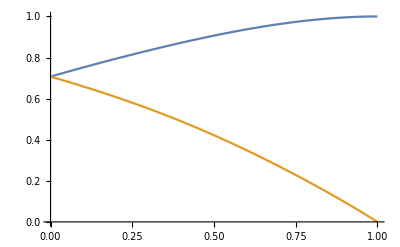

```mathematica
ListLinePlot[{{dataα[[All,1,3]],SchmidtCoefficientsααlist[[All,1]]}ᵀ,{dataα[[All,1,3]],SchmidtCoefficientsααlist[[All,2]]}ᵀ}]
```

```mathematica
Select[dataαβSCs[[2]],#[[1]]==#[[2]]&]
```

{{0.,0.,0.707107},{0.05,0.05,0.683646},{0.1,0.1,0.659514},{0.15,0.15,0.6348},{0.2,0.2,0.6096},{0.25,0.25,0.584014},{0.3,0.3,0.558144},{0.35,0.35,0.532095},{0.4,0.4,0.505969},{0.45,0.45,0.479861},{0.5,0.5,0.453862},{0.55,0.55,0.42805},{0.6,0.6,0.402491},{0.65,0.65,0.377236},{0.7,0.7,0.352318},{0.75,0.75,0.327754},{0.8,0.8,0.303543},{0.85,0.85,0.279663},{0.9,0.9,0.256075},{0.95,0.95,0.232722},{1.,1.,0.209526}}

```mathematica
Export["schmidt1.mat",{dataα[[All,1,3]],SchmidtCoefficientsααlist[[All,1]]}ᵀ]
Export["schmidt2.mat",{dataα[[All,1,3]],SchmidtCoefficientsααlist[[All,2]]}ᵀ]
```

schmidt1.mat

schmidt2.mat

## 4. Analytical expressions

For the analytical expression, the coefficient of the characteristic polynomial are:
 γ_0=(α^2-β^2)^2-8(α^2(a^2-a^2 b+b)+β^2(b^2-b^2 a+a)-2(b^2+a^2-a^2 b^2));
γ_1=8α β(a b-a - b- 1);
γ_2=-2(4+ α^2+β^2);
γ_3=0;γ_4=1;

```mathematica
CheckCoeff=Module[{γ,a,b,α,β},
Subscript[γ, 0]=(α^2-β^2)^2-8(α^2(a^2-a^2 b+b)+β^2(b^2-b^2 a+a)-2(b^2+a^2-a^2 b^2));
Subscript[γ, 1]=8α β(a b-a - b- 1);
Subscript[γ, 2]=-2(4+ α^2+β^2);
Subscript[γ, 3]=0;Subscript[γ, 4]=1;
Collect[CharacteristicPolynomial[𝒞[a,b,α,β],λ],λ]==∑_(k=0)^4 Subscript[γ, k] λ^k//FullSimplify
]
```

True

```mathematica
sol=Solve[λ^4+Subscript[γ, 2] λ^2+Subscript[γ, 1] λ+Subscript[γ, 0]==0,λ]/.{(27 Subscript[γ, 1]^2-72 Subscript[γ, 0] Subscript[γ, 2]+2 Subscript[γ, 2]^3+√(-4 (12 Subscript[γ, 0]+Subscript[γ, 2]^2)^3+(27 Subscript[γ, 1]^2-72 Subscript[γ, 0] Subscript[γ, 2]+2 Subscript[γ, 2]^3)^2))->ξ}
```

{{λ→1/2 √(ξ^(1/3)/(3 2^(1/3))-(2 γ_2)/3+(2^(1/3) (12 γ_0+γ_2^2))/(3 ξ^(1/3)))-1/2 √(-ξ^(1/3)/(3 2^(1/3))-(4 γ_2)/3-(2^(1/3) (12 γ_0+γ_2^2))/(3 ξ^(1/3))-(2 γ_1)/(√(ξ^(1/3)/(3 2^(1/3))-(2 γ_2)/3+(2^(1/3) (12 γ_0+γ_2^2))/(3 ξ^(1/3)))))},{λ→1/2 √(ξ^(1/3)/(3 2^(1/3))-(2 γ_2)/3+(2^(1/3) (12 γ_0+γ_2^2))/(3 ξ^(1/3)))+1/2 √(-ξ^(1/3)/(3 2^(1/3))-(4 γ_2)/3-(2^(1/3) (12 γ_0+γ_2^2))/(3 ξ^(1/3))-(2 γ_1)/(√(ξ^(1/3)/(3 2^(1/3))-(2 γ_2)/3+(2^(1/3) (12 γ_0+γ_2^2))/(3 ξ^(1/3)))))},{λ→-1/2 √(ξ^(1/3)/(3 2^(1/3))-(2 γ_2)/3+(2^(1/3) (12 γ_0+γ_2^2))/(3 ξ^(1/3)))-1/2 √(-ξ^(1/3)/(3 2^(1/3))-(4 γ_2)/3-(2^(1/3) (12 γ_0+γ_2^2))/(3 ξ^(1/3))+(2 γ_1)/(√(ξ^(1/3)/(3 2^(1/3))-(2 γ_2)/3+(2^(1/3) (12 γ_0+γ_2^2))/(3 ξ^(1/3)))))},{λ→-1/2 √(ξ^(1/3)/(3 2^(1/3))-(2 γ_2)/3+(2^(1/3) (12 γ_0+γ_2^2))/(3 ξ^(1/3)))+1/2 √(-ξ^(1/3)/(3 2^(1/3))-(4 γ_2)/3-(2^(1/3) (12 γ_0+γ_2^2))/(3 ξ^(1/3))+(2 γ_1)/(√(ξ^(1/3)/(3 2^(1/3))-(2 γ_2)/3+(2^(1/3) (12 γ_0+γ_2^2))/(3 ξ^(1/3)))))}}

```mathematica
(sol/.{ξ^(1/3)/(3 2^(1/3))-(2 Subscript[γ, 2])/3+(2^(1/3) (12 Subscript[γ, 0]+Subscript[γ, 2]^2))/(3 ξ^(1/3))->ζ})/.-ξ^(1/3)/(3 2^(1/3))-(4 Subscript[γ, 2])/3-(2^(1/3) (12 Subscript[γ, 0]+Subscript[γ, 2]^2))/(3 ξ^(1/3))->κ
```

{{λ→(√ζ)/2-1/2 √(κ-(2 γ_1)/(√ζ))},{λ→(√ζ)/2+1/2 √(κ-(2 γ_1)/(√ζ))},{λ→-(√ζ)/2-1/2 √(κ+(2 γ_1)/(√ζ))},{λ→-(√ζ)/2+1/2 √(κ+(2 γ_1)/(√ζ))}}

This is a nice way to write the roots of the determinant. λ→±_t(√ζ)/2±_s 1/2 √(κ∓_t(2 γ_1)/(√ζ))
From the following equation we want to determine the largest eigenvalue. We observe that the eigenvalues are of the kind
λ_1=(√ζ)/2-1/2 √(κ-(2 γ_1)/(√ζ))
λ_2=(√ζ)/2+1/2 √(κ-(2 γ_1)/(√ζ))
λ_3=-(√ζ)/2-1/2 √(κ+(2 γ_1)/(√ζ))
λ_2=-(√ζ)/2+1/2 √(κ+(2 γ_1)/(√ζ))
with γ_1<0, therefore the largest eigenvalue is λ_2=(√ζ)/2+1/2 √(κ-(2 γ_1)/(√ζ)).

This is a depressed quartic equation (see https://en.wikipedia.org/wiki/Quartic_equation)

A different parametrization in the following. Given
A_1[θ_]:= Cos[θ]σ_3+Sin[θ]σ_1
CHSH[η_,θ_]:=σ_3⊙ σ_3 +  σ_3⊙ A_1[θ]+A_1[θ]⊙ σ_3-A_1[θ]⊙ A_1[θ]+ η (σ_3⊙ σ_0+ σ_0⊙ σ_3)
we compute the determinant
FullSimplify[Det[CHSH[η,θ]-λ IdentityMatrix[4]]]
and we obtain
(λ+2 Cos[θ])(λ^3+b λ^2+c λ+d)=0 with 
b=-2  Cos[θ];
c=(-6-4 η^2+2 Cos[2 θ]);
d=-4 η^2+10 Cos[θ]-8 η^2 Cos[θ]+4 η^2 Cos[2 θ]-2 Cos[3 θ]; 
and p=(3 a c -b^2)/(3 a^2);q=(2 b^3-9a b c +27 a^2 d)/(27 a^3);
the solutions are
t1=2 √(-p/3)Cos[1/3 ArcCos[(3q)/(2p)√(-3/p)]-(2π)/3]-b/3;
t2=2 √(-p/3)Cos[1/3 ArcCos[(3q)/(2p)√(-3/p)]-2(2π)/3]-b/3;
t3=2 √(-p/3)Cos[1/3 ArcCos[(3q)/(2p)√(-3/p)]-3(2π)/3]-b/3;
t4=√(-p/3)Cos[1/3 ArcCos[(3q)/(2p)√(-3/p)]-4(2π)/3]-b/3
t4, the largest  can be rewritten as
t[θ,η]=2/3 √g[θ,η] Cos[1/3 ArcCos[f[θ,η]]]+(2 Cos[θ])/3 with 
g[θ_,η_]:=4 Cos[θ]^2-3(-6-4 η^2+2 Cos[2 θ])
f[θ_,η_]:=4 (1/g[θ,η])^(3/2) (3 (-7+12 η^2) Cos[θ]+5 Cos[3 θ]+27 η^2 Sin[θ]^2)

now we can do the same with α and a parametrization so that 
-16 a+8 a^3+8 α^2+8 a α^2-8 a^2 α^2+(8-4 a^2+4 α^2) λ+2 a λ^2-λ^3=0 becomes
γ_3 λ^3+γ_2 λ^2+γ_1 λ+γ_0=0 with
γ_3=-1,
γ_2=2a,	
γ_1=4(2- a^2+ α^2),
γ_0=8(-2 a+ a^3+ α^2+ a α^2- a^2 α^2)
the new p and q are
p=(3  γ_1 -γ_2^2)/(3 γ_3^2);q=(2 γ_2^3-9 γ_3 γ_2 γ_1 +27 γ_3^2 γ_0)/(27 γ_3^3);
and the highest root is
t=√(-p/3)Cos[1/3 ArcCos[(3q)/(2p)√(-3/p)]-3(2π)/3]-b/3

```mathematica
Clear[a]
```

```mathematica
FullSimplify[Det[𝒞[a,a,α,α]-λ IdentityMatrix[4]]]
```

-((2 a+λ) (8 a^3+8 λ-λ^3+4 α^2 (2+λ)-4 a^2 (2 α^2+λ)+2 a (-8+4 α^2+λ^2)))

```mathematica
Collect[(8 a^3+8 λ-λ^3+4 α^2 (2+λ)-4 a^2 (2 α^2+λ)+2 a (-8+4 α^2+λ^2)),λ]
```

```mathematica
Solve[-16 a+8 a^3+8 α^2+8 a α^2-8 a^2 α^2+(8-4 a^2+4 α^2) λ+2 a λ^2-λ^3==0,λ]
```

{{λ→(2 a)/3+(2^(1/3) (-24+8 a^2-12 α^2))/(3 (288 a-160 a^3-216 α^2-288 a α^2+216 a^2 α^2+√(4 (-24+8 a^2-12 α^2)^3+(288 a-160 a^3-216 α^2-288 a α^2+216 a^2 α^2)^2))^(1/3))-1/(3 2^(1/3))(288 a-160 a^3-216 α^2-288 a α^2+216 a^2 α^2+√(4 (-24+8 a^2-12 α^2)^3+(288 a-160 a^3-216 α^2-288 a α^2+216 a^2 α^2)^2))^(1/3)},{λ→(2 a)/3-((1+ⅈ √3) (-24+8 a^2-12 α^2))/(3 2^(2/3) (288 a-160 a^3-216 α^2-288 a α^2+216 a^2 α^2+√(4 (-24+8 a^2-12 α^2)^3+(288 a-160 a^3-216 α^2-288 a α^2+216 a^2 α^2)^2))^(1/3))+1/(6 2^(1/3))(1-ⅈ √3) (288 a-160 a^3-216 α^2-288 a α^2+216 a^2 α^2+√(4 (-24+8 a^2-12 α^2)^3+(288 a-160 a^3-216 α^2-288 a α^2+216 a^2 α^2)^2))^(1/3)},{λ→(2 a)/3-((1-ⅈ √3) (-24+8 a^2-12 α^2))/(3 2^(2/3) (288 a-160 a^3-216 α^2-288 a α^2+216 a^2 α^2+√(4 (-24+8 a^2-12 α^2)^3+(288 a-160 a^3-216 α^2-288 a α^2+216 a^2 α^2)^2))^(1/3))+1/(6 2^(1/3))(1+ⅈ √3) (288 a-160 a^3-216 α^2-288 a α^2+216 a^2 α^2+√(4 (-24+8 a^2-12 α^2)^3+(288 a-160 a^3-216 α^2-288 a α^2+216 a^2 α^2)^2))^(1/3)}}

```mathematica
Clear[checkt1t2]
```

```mathematica
checkt1t2=Module[{a,b,c,d,p,q,g,f,t1,t2},
a=1;
b=-2  Cos[θ];
c=(-6-4 η^2+2 Cos[2 θ]);
d=-4 η^2+10 Cos[θ]-8 η^2 Cos[θ]+4 η^2 Cos[2 θ]-2 Cos[3 θ];
λ^3+b λ^2+c λ+d;
p=(3 a c -b^2)/(3 a^2);
q=(2 b^3-9a b c +27 a^2 d)/(27 a^3);
t1=2 √(-p/3)Cos[1/3 ArcCos[(3q)/(2p)√(-3/p)]-3(2π)/3]-b/3;
g=4 Cos[θ]^2-3(-6-4 η^2+2 Cos[2 θ]);
f=4 (1/g)^(3/2) (3 (-7+12 η^2) Cos[θ]+5 Cos[3 θ]+27 η^2 Sin[θ]^2);
t2=2/3 √g Cos[1/3 ArcCos[f]]+(2 Cos[θ])/3;
FullSimplify[t1-t2]
]
```

0

## 5. Main figure

Caption: Optimal quantum value (On the top-left), Schmidt coefficient (on the bottom-left) and optimal settings

```mathematica
size=380;GraphicsGrid[{{Labeled[Show[cqplot,ImageSize->size],MaTeX["(a)",Magnification->1.5]],Labeled[Show[ca2D,ImageSize->size],MaTeX["(b)",Magnification->1.5]],Labeled[Show[cb2D,ImageSize->size],MaTeX["(c)",Magnification->1.5]]},{Labeled[Show[schmidtplot,ImageSize->size],MaTeX["(d)",Magnification->1.5]],Labeled[Show[ca3D,ImageSize->size],MaTeX["(e)",Magnification->1.5]],Labeled[Show[cb3D,ImageSize->size],MaTeX["(f)",Magnification->1.5]]}},Spacings->{0,0},ImageSize->Full]
```

-Graphics-

```mathematica
subfig[plot_,label_]:=Labeled[Show[plot,ImageSize->size],MaTeX[label,Magnification->1.5]]
size=380;
GraphicsGrid[{{Labeled[Show[cqplot,ImageSize->size],MaTeX["(a)",Magnification->1.5]],Labeled[Show[ca2D,ImageSize->size],MaTeX["(b)",Magnification->1.5]],Labeled[Show[cb2D,ImageSize->size],MaTeX["(c)",Magnification->1.5]]},{Labeled[Show[schmidtplot,ImageSize->size],MaTeX["(d)",Magnification->1.5]],Labeled[Show[ca3D,ImageSize->size],MaTeX["(e)",Magnification->1.5]],Labeled[Show[cb3D,ImageSize->size],MaTeX["(f)",Magnification->1.5]]}},Spacings->{0,0},ImageSize->Full]
```

-Graphics-

```mathematica
GraphicsGrid[{{subfig[cqplot,"(a)"],subfig[schmidtplot,"(b)"],subfig[ca3D,"(c)"]},{subfig[eigesplot,"(d)"],subfig[entplot,"(e)"],subfig[cb3D,"(f)"]}},Spacings->{0,0},ImageSize->Full]
```

-Graphics-